```mathematica
s = Import["wt_data.csv","CSV",Path->NotebookDirectory[],"HeaderLines"->1];
```

```mathematica
Dimensions[s];
```

```mathematica
data = Import["pdata.csv",Path-> "/home/king/Dropbox/GitHub/microgrid_sim/mathematica_solver"]
```

{{20100101 00:00,0,405,10072,10299,10193,107,197,82,537,77,-9,340,188,245,81,390,245,151,103,262,43,32,7,223,6,209},{20100101 01:00,0,408,10076,10301,10191,125,209,77,540,50,-20,340,186,242,70,379,242,148,102,262,43,47,7,218,6,215},«8755»,{20101231 22:00,0,396,10071,10301,10195,112,191,76,583,38,-4,340,195,254,90,390,254,160,106,256,42,23,7,240,6,197},{20101231 23:00,0,400,10070,10301,10194,145,188,81,544,43,-4,340,192,250,81,390,250,157,104,259,43,23,7,217,6,213}}

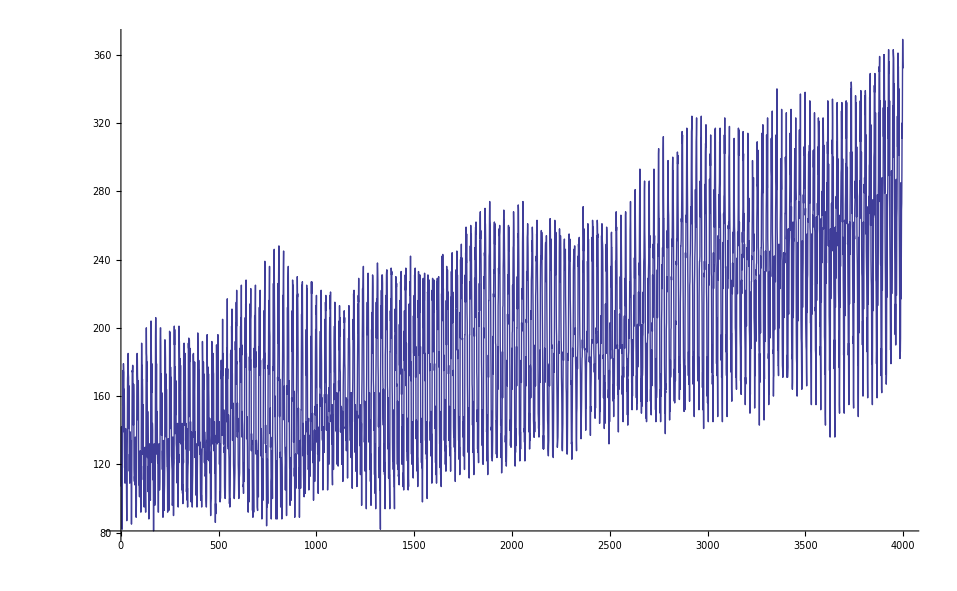

```mathematica
ListPlot[{s[[1;;4000,7]]},Joined->True]
```

```mathematica
DateList[{"2010-12-31 23:00:00",{"Year","-","Month","-","Day"," ","Hour",":","Minute",":","Second"}}]
```

{2010,12,31,23,0,0.}

```mathematica
s[[All,20]]
```

{103,102,100,100,99,99,98,99,100,109,114,119,122,120,120,120,115,110,108,108,109,107,106,104,103,102,100,100,99,99,97,98,100,108,113,119,121,120,120,119,115,111,109,108,109,108,107,105,105,103,102,101,100,100,98,99,101,109,115,121,122,122,122,122,117,112,110,111,111,110,109,107,106,106,103,103,102,102,100,101,102,110,116,122,123,123,123,123,118,114,111,111,111,110,110,107,106,105,102,102,101,101,99,100,102,110,116,121,123,123,123,123,119,114,111,112,112,111,110,107,106,105,102,102,102,102,100,101,103,110,117,121,123,123,123,123,119,115,112,113,113,113,110,108,107,106,103,103,103,103,102,102,104,112,118,121,123,123,123,124,121,115,113,114,113,114,110,108,107,106,103,102,102,102,101,101,104,111,117,121,123,124,124,124,121,116,113,114,113,114,111,108,106,105,103,102,101,102,100,101,104,112,118,122,123,125,125,125,122,117,114,114,114,115,112,109,107,106,103,103,102,101,101,101,104,112,118,122,124,125,125,124,123,117,114,115,114,115,113,110,108,107,104,103,103,102,102,102,104,112,119,123,124,126,125,123,122,117,114,114,114,115,112,110,107,106,103,103,103,102,102,102,104,112,118,122,124,126,125,123,121,115,113,113,113,114,111,108,106,105,103,103,103,102,102,102,104,113,118,121,124,125,124,122,120,114,112,113,112,113,111,108,106,105,104,103,104,102,102,102,105,113,119,122,124,126,125,123,121,115,113,114,115,116,114,109,107,107,106,103,104,103,103,103,106,113,119,123,124,126,126,124,121,116,115,115,116,116,114,110,108,107,106,104,104,102,103,103,106,114,120,123,124,126,126,124,122,116,115,116,117,118,115,110,108,107,107,105,104,102,103,104,107,115,121,123,124,127,126,124,122,116,114,115,116,116,115,110,107,106,107,105,104,103,103,104,108,116,121,123,124,127,126,123,122,116,114,114,114,115,113,109,106,105,106,102,103,101,102,103,106,114,119,123,124,127,126,123,123,117,115,114,115,115,113,109,107,107,107,104,104,102,103,104,107,115,119,123,124,128,127,123,122,117,114,113,114,114,113,109,107,107,107,103,103,102,102,104,108,115,119,124,125,128,127,124,122,117,114,112,113,113,113,109,106,105,106,103,102,101,102,104,107,115,118,123,125,128,127,123,122,117,114,112,113,112,113,109,107,106,106,103,103,102,103,105,108,116,119,124,126,128,127,124,122,118,115,113,113,113,114,110,108,106,106,103,103,102,104,105,108,115,118,124,126,128,127,125,122,118,114,114,113,113,114,109,107,105,106,103,104,102,103,104,107,114,117,123,125,127,126,125,121,118,114,113,112,112,112,108,105,103,104,101,102,100,101,103,106,112,116,122,124,126,125,125,121,117,113,113,112,111,112,107,105,103,103,101,102,100,102,103,106,111,116,122,124,126,126,126,122,118,114,113,112,112,112,109,106,104,104,102,102,101,102,104,106,112,117,123,124,127,126,125,122,118,113,113,111,111,111,108,105,103,103,101,102,100,102,104,106,112,116,123,125,127,127,126,122,118,113,112,110,110,109,107,104,103,102,101,102,100,101,104,106,111,116,123,125,126,126,125,122,118,113,111,109,108,108,107,103,102,102,100,101,100,101,102,105,110,115,121,123,125,125,124,121,117,112,110,108,107,107,105,102,101,100,98,100,99,100,102,104,111,115,121,123,125,125,125,122,118,112,110,108,108,106,106,102,101,100,98,100,98,100,101,103,109,113,119,121,123,124,124,122,117,111,108,108,107,106,105,102,101,100,98,100,98,100,100,103,110,115,119,122,123,123,124,121,117,110,108,108,107,106,104,101,100,99,98,99,97,99,100,103,109,115,120,122,123,124,124,122,117,112,110,110,108,107,105,102,101,99,98,99,97,100,100,103,110,116,121,122,124,124,125,123,118,112,110,110,108,107,105,102,101,99,99,99,97,99,98,102,110,117,121,123,126,125,126,124,118,112,110,110,108,106,103,100,100,98,97,98,96,97,98,102,110,117,121,124,127,126,127,125,119,113,110,111,109,105,103,101,100,98,98,97,96,97,98,102,110,118,121,124,127,126,127,125,119,113,109,111,108,105,103,100,100,97,98,97,96,97,98,103,112,119,122,124,128,128,128,127,120,114,109,111,109,106,104,102,100,98,99,98,97,98,99,104,113,120,123,125,129,129,130,129,122,115,110,112,110,107,105,102,101,99,99,99,98,99,100,104,114,121,124,125,128,128,129,129,121,115,110,111,109,106,104,102,100,97,98,98,97,98,98,104,113,121,123,126,129,129,130,130,122,115,109,111,108,105,103,101,99,96,97,97,96,96,97,102,112,120,122,124,128,128,130,129,121,114,109,110,108,105,103,101,98,97,97,97,95,96,96,102,112,120,122,123,129,128,130,129,121,114,108,111,109,104,103,101,97,97,97,96,95,96,96,102,112,120,123,124,129,128,130,130,122,116,109,111,110,105,103,101,98,96,97,96,95,95,96,101,111,119,122,123,127,126,128,130,123,117,110,111,109,105,103,101,98,97,97,96,95,95,97,103,113,122,123,125,128,128,130,131,125,118,110,111,109,104,103,101,97,96,97,95,95,95,97,102,113,121,123,124,127,128,129,130,124,117,110,110,108,103,103,100,97,96,97,96,96,96,97,103,113,121,122,124,127,127,128,131,125,116,108,108,107,103,102,99,96,96,97,97,96,96,98,103,114,120,123,124,127,128,128,130,124,116,107,107,106,101,101,98,96,96,96,98,97,97,99,104,114,121,123,123,127,127,128,131,124,116,108,107,106,102,103,100,98,97,98,99,98,98,99,105,114,121,122,123,126,127,128,131,124,115,107,106,105,102,102,99,97,96,97,98,97,97,99,106,115,120,123,123,127,128,128,131,123,115,107,105,105,102,103,99,98,96,97,98,97,97,99,105,114,119,123,123,126,127,127,130,124,115,107,105,105,101,102,98,97,96,96,97,96,96,98,104,113,118,122,123,126,127,127,130,123,115,107,106,104,101,102,98,97,96,95,97,96,96,97,104,113,117,122,123,127,127,128,130,125,116,107,106,104,101,101,98,97,96,95,96,96,96,98,105,113,117,124,124,128,128,129,131,125,117,108,107,106,102,102,99,98,97,97,97,97,97,99,106,114,119,125,125,128,129,129,131,125,116,108,106,104,101,101,98,99,97,96,97,98,98,100,108,115,120,126,126,129,131,130,132,127,118,110,107,106,104,103,100,101,98,97,98,99,99,101,108,115,121,126,126,129,131,130,132,126,117,109,107,105,104,103,99,100,98,97,98,99,100,101,108,116,122,127,127,131,132,132,134,128,118,110,107,106,105,103,100,101,100,98,99,100,100,101,109,115,121,128,128,132,132,133,134,129,118,111,108,107,105,102,100,102,100,98,99,99,99,100,109,115,120,128,129,132,133,134,134,128,118,111,107,107,106,102,99,102,100,98,99,99,99,100,109,116,121,129,129,132,134,134,134,128,118,111,107,107,105,102,99,101,99,97,96,97,97,99,108,116,122,129,130,133,135,135,135,130,120,113,108,108,105,102,99,100,99,97,96,97,98,99,109,117,123,130,131,133,135,135,135,130,120,113,108,107,105,101,98,100,99,97,96,97,98,99,110,118,123,131,132,133,136,136,136,132,122,114,108,107,104,100,97,99,99,96,96,98,98,100,110,118,124,130,132,133,136,137,137,133,122,114,108,106,103,98,96,99,99,95,96,97,97,99,110,118,123,129,131,133,135,136,135,132,122,114,108,106,104,100,97,100,100,97,97,98,98,101,111,119,124,130,131,133,135,136,135,131,122,114,108,106,104,100,97,100,100,97,97,97,97,101,110,118,123,129,131,133,136,136,135,131,123,114,108,106,104,100,97,99,100,98,98,99,102,112,120,125,130,132,134,136,137,137,132,123,114,107,106,104,100,97,99,99,97,98,98,99,101,112,120,125,130,132,134,136,137,137,133,123,113,107,105,103,100,97,99,99,97,97,97,97,100,111,120,124,129,132,132,134,136,137,133,122,112,106,104,101,99,95,97,97,96,95,95,95,98,111,118,123,128,132,132,135,137,137,133,122,112,106,105,101,98,96,97,97,96,95,95,95,99,112,120,124,130,133,134,137,139,137,133,123,112,107,106,102,99,96,97,95,96,95,95,95,99,112,120,125,129,133,133,136,138,138,132,124,113,108,106,102,100,96,97,95,96,94,95,95,99,112,119,124,128,131,133,135,137,137,132,124,112,107,105,101,100,97,97,95,96,95,94,95,99,112,119,124,129,132,134,136,137,137,132,124,112,107,105,101,101,97,98,95,96,95,94,95,99,112,118,123,128,130,132,135,137,136,131,123,111,107,105,101,100,96,97,95,96,95,93,94,99,111,118,121,127,129,132,133,136,136,131,123,110,106,104,100,100,97,97,95,95,94,94,94,99,111,117,121,127,129,132,134,136,136,131,123,110,107,106,102,102,98,98,96,96,95,94,95,99,111,117,121,128,129,132,134,136,137,131,123,109,107,106,102,103,99,98,96,96,95,93,95,100,112,118,122,129,131,133,135,138,139,132,123,110,107,107,103,102,99,99,96,96,95,93,95,100,113,119,124,130,132,134,137,139,140,133,124,111,108,108,103,103,100,99,96,96,95,94,96,101,114,120,126,131,133,135,138,139,141,134,124,111,107,107,103,102,100,98,95,95,94,92,94,100,113,119,126,131,133,134,139,140,142,134,126,112,109,109,104,104,100,99,97,96,95,93,95,102,115,121,128,132,134,136,140,142,144,136,127,114,110,110,104,103,100,99,97,96,95,94,96,103,116,123,130,133,136,138,142,145,145,138,129,115,111,111,104,105,101,100,97,96,96,94,97,105,117,125,131,135,137,139,143,145,145,137,128,114,110,108,103,103,100,100,97,96,95,94,97,105,116,123,130,134,135,137,140,141,143,135,126,112,108,106,100,100,98,98,96,95,95,93,96,105,117,124,130,134,134,137,141,142,143,135,127,112,107,106,100,100,98,97,96,94,95,93,96,106,118,125,132,135,135,138,142,143,144,136,127,113,109,106,101,101,99,98,96,95,95,93,97,106,118,126,132,134,135,137,142,143,145,136,127,114,110,107,101,99,98,97,96,95,96,94,97,107,119,127,134,134,136,138,143,144,144,136,128,114,109,106,102,100,99,97,96,95,96,94,97,107,120,127,135,134,137,138,143,144,144,137,128,113,109,106,101,99,98,96,96,95,96,93,96,106,119,127,134,134,137,138,143,143,143,136,126,113,108,105,100,99,97,96,95,95,96,93,95,108,120,128,136,135,138,139,144,144,143,136,127,115,110,107,101,100,99,97,97,96,97,95,96,108,121,129,136,135,137,139,144,144,143,135,127,114,108,105,99,98,96,94,94,95,95,93,95,107,119,129,135,134,137,138,143,143,142,135,126,113,108,104,98,97,94,93,93,93,94,92,94,106,118,127,133,133,135,138,141,142,141,134,126,113,108,103,98,97,94,93,93,93,94,92,94,106,118,126,132,132,134,137,140,141,139,133,124,111,107,102,97,95,93,91,92,91,92,91,93,106,117,125,131,132,135,137,139,140,137,132,123,110,106,101,96,94,92,89,90,90,91,90,93,105,115,123,129,130,133,135,137,137,135,130,122,109,105,100,96,92,92,89,89,90,91,90,93,105,116,124,129,130,133,136,138,138,137,131,124,110,106,101,96,93,92,88,89,90,92,91,94,105,117,124,131,131,134,137,140,140,139,133,126,112,106,102,97,95,94,90,91,91,91,91,94,105,117,124,131,131,134,137,140,139,138,133,125,112,106,101,96,94,93,89,90,90,91,91,94,105,116,124,130,130,134,137,139,140,138,134,126,111,106,100,95,94,92,88,90,89,91,90,94,106,117,124,130,131,134,137,140,140,139,134,126,111,104,100,94,93,91,87,88,88,89,89,93,105,116,122,128,130,133,137,141,139,139,135,127,111,103,100,94,92,90,87,88,88,89,89,93,106,116,122,129,130,133,137,141,140,139,135,127,113,104,100,95,92,91,88,88,88,90,90,94,107,117,123,128,130,132,136,139,140,138,135,126,112,104,99,93,90,89,87,87,87,88,88,93,105,116,121,127,129,132,136,139,140,138,136,126,111,102,97,91,87,87,84,85,85,86,87,91,104,114,120,126,128,131,135,139,140,138,136,126,112,102,97,91,87,86,84,86,85,85,87,92,104,115,120,125,127,131,135,138,139,137,135,126,110,101,96,90,86,86,83,85,84,84,86,91,104,114,120,125,128,131,135,139,140,138,135,126,111,101,97,91,87,86,84,86,84,84,86,91,104,114,120,125,128,131,134,139,140,138,136,127,112,101,97,91,86,85,84,85,84,83,85,90,102,113,118,123,126,129,132,139,140,138,135,127,112,101,97,92,87,87,85,86,85,83,86,90,103,114,118,123,126,129,132,138,140,137,135,127,113,102,98,93,88,87,86,86,84,83,86,91,103,113,117,122,125,128,132,138,140,137,135,126,112,102,98,93,88,87,85,86,84,82,86,90,103,113,117,121,125,128,132,138,140,136,134,125,111,101,97,93,87,86,84,85,83,81,85,89,102,111,116,120,125,129,132,137,140,136,134,125,111,101,97,93,88,87,85,86,85,83,86,90,103,112,116,121,126,130,132,138,140,136,133,125,110,101,98,93,88,86,84,86,84,81,85,89,101,110,114,120,124,128,131,137,139,135,132,123,110,101,99,93,89,87,85,86,84,82,85,90,102,111,114,120,124,128,131,136,139,135,132,123,110,101,98,93,89,85,83,85,83,81,84,90,102,110,115,119,124,128,132,136,139,135,132,124,109,101,97,92,88,85,82,84,81,80,82,89,101,109,113,119,124,129,132,136,139,135,131,122,108,100,96,91,87,84,81,82,80,79,81,87,99,108,111,117,121,126,129,133,137,133,129,122,106,99,95,92,88,85,82,82,80,79,82,87,100,108,111,118,122,126,129,133,137,134,130,122,106,100,96,93,90,87,84,83,81,81,82,88,101,109,112,120,123,127,130,134,138,135,132,122,108,101,96,93,91,87,85,83,82,82,83,89,101,109,112,120,121,126,130,133,137,134,131,121,107,100,94,91,89,85,82,80,80,79,82,88,101,108,111,119,120,126,129,132,136,133,130,120,106,99,93,89,87,85,81,80,80,79,80,87,100,107,111,117,119,124,129,130,135,133,129,119,105,98,92,87,86,82,79,78,78,77,78,86,99,106,110,117,119,124,129,130,135,134,130,119,104,97,90,85,84,81,77,77,76,75,76,85,97,105,109,117,118,123,128,129,134,132,129,118,104,97,89,85,83,80,77,76,76,75,76,84,96,104,109,116,118,122,127,129,134,132,130,118,106,98,89,84,83,79,77,76,76,74,76,84,96,105,109,115,117,121,126,128,132,131,128,117,105,96,87,83,81,77,75,74,73,71,74,82,95,103,108,114,117,120,124,126,131,130,127,116,104,94,85,82,79,76,74,72,73,71,73,82,94,102,107,113,117,119,124,124,130,129,126,115,104,94,83,81,78,75,74,71,71,70,71,81,94,101,107,113,116,119,123,124,129,128,126,115,103,93,83,81,78,75,74,71,71,69,71,80,93,100,105,112,115,118,122,123,128,127,125,114,102,92,82,79,76,74,72,70,71,69,70,79,92,99,105,111,114,118,121,123,127,127,123,114,102,92,81,79,76,73,73,71,72,69,71,80,92,99,106,112,114,119,121,124,127,126,122,113,102,91,81,78,74,72,72,69,70,67,69,79,91,98,104,110,113,117,119,123,126,125,121,112,101,90,80,77,72,69,70,67,68,66,68,77,89,97,102,108,112,116,118,121,124,123,119,111,100,89,80,76,71,69,69,66,67,65,67,77,89,97,102,108,111,115,118,121,124,123,119,112,100,88,79,75,70,68,68,66,67,65,66,76,87,95,100,107,110,114,117,120,123,122,118,111,100,88,78,75,69,68,68,66,66,66,66,76,88,95,100,107,110,114,117,121,123,122,119,111,100,87,78,75,69,68,68,65,66,66,67,76,87,95,101,107,110,114,117,122,123,121,118,111,99,87,78,75,69,68,67,65,67,66,67,76,87,94,100,107,111,114,117,122,122,121,118,110,99,87,78,75,70,68,68,65,66,65,66,75,87,94,99,107,110,113,115,120,121,120,116,109,97,86,78,75,69,68,68,65,66,65,66,75,87,93,98,106,109,113,115,120,121,120,117,109,97,86,78,75,69,68,68,65,65,65,65,74,86,92,97,105,108,112,116,120,120,120,117,109,97,86,78,74,68,67,66,64,65,64,64,73,84,91,96,104,107,111,115,120,120,120,117,109,97,86,78,74,68,67,66,64,65,63,66,72,83,91,95,103,107,111,114,120,119,120,116,109,96,85,77,73,68,67,65,63,64,63,65,71,83,90,95,102,106,110,113,119,118,118,116,108,96,85,77,74,69,67,65,63,64,64,64,72,82,90,95,103,107,110,114,119,119,120,117,109,97,86,78,74,68,67,65,63,64,63,64,72,83,89,95,103,107,110,115,119,119,120,119,109,97,86,77,75,69,67,65,64,65,64,65,73,83,90,96,103,108,110,115,119,118,120,118,109,97,86,77,75,70,68,66,64,65,63,65,73,83,89,95,102,108,110,114,119,118,119,117,108,97,86,76,74,70,67,65,64,65,63,64,72,83,88,95,102,107,110,114,119,119,119,115,107,96,86,77,75,72,68,66,65,65,63,65,73,84,89,96,104,108,111,115,120,119,119,115,108,96,86,77,76,73,68,67,66,66,63,65,73,83,89,96,104,108,111,114,119,119,119,116,108,96,86,77,75,72,68,66,66,65,63,65,72,83,89,96,103,107,111,113,119,119,119,116,108,97,86,77,75,72,68,66,65,65,63,66,71,82,88,95,102,105,110,113,119,118,118,115,107,96,84,75,74,71,66,64,64,64,63,65,71,81,87,93,101,104,109,112,118,118,117,114,107,95,83,74,72,70,66,64,63,63,62,64,70,80,86,93,100,103,109,112,117,118,116,113,106,95,83,75,72,70,66,63,63,62,62,64,69,80,85,93,101,102,109,110,117,117,115,112,106,95,83,74,72,71,66,64,63,63,62,65,70,81,85,94,101,102,109,111,116,118,116,111,106,95,83,74,71,71,66,63,63,62,61,63,70,80,85,93,100,102,109,110,115,117,115,110,105,94,83,74,71,71,66,64,63,62,61,64,70,80,86,94,102,104,111,111,116,118,115,111,107,96,84,75,71,71,67,64,63,62,61,64,70,81,86,93,101,103,110,111,115,117,115,111,107,95,82,75,70,71,66,63,63,60,61,63,70,81,86,92,100,102,110,110,114,116,114,110,107,95,83,75,70,70,66,62,63,60,60,62,69,80,86,92,100,101,110,110,114,116,114,110,107,95,82,74,69,69,65,61,63,59,60,61,68,80,86,92,99,100,109,109,115,116,114,110,107,95,82,74,69,69,65,62,62,59,60,61,68,79,86,92,99,100,109,109,115,116,114,110,107,95,82,74,69,68,64,61,61,59,60,61,68,79,86,93,99,102,109,109,115,117,115,111,108,96,83,75,70,68,65,62,62,60,61,62,69,80,87,92,98,102,109,110,116,117,116,112,108,96,83,76,71,68,65,62,62,60,61,61,69,81,87,93,99,103,109,110,116,117,115,111,108,96,83,75,70,68,65,62,62,60,60,60,69,80,88,93,99,103,109,110,115,117,115,111,108,96,83,75,70,67,64,61,62,60,60,59,69,81,88,94,99,103,108,110,116,117,116,112,109,97,83,75,71,67,65,61,62,60,60,59,70,80,88,93,99,104,108,111,116,117,116,112,109,96,83,75,71,67,64,61,62,60,60,59,70,80,88,94,100,104,108,111,116,117,117,113,109,96,84,76,71,66,64,61,61,59,60,59,70,79,88,93,99,103,107,111,116,116,116,113,109,96,83,76,71,66,63,61,61,60,61,59,69,79,88,94,99,104,107,112,116,116,118,115,109,96,84,76,71,65,62,60,60,59,60,59,70,79,88,93,98,103,106,111,116,117,118,115,108,95,83,75,71,65,62,60,60,60,59,58,69,79,88,93,99,103,106,111,116,117,118,114,108,95,82,74,71,65,62,60,60,60,59,58,68,77,87,92,99,103,106,111,115,118,118,114,108,95,81,74,70,65,62,60,59,60,59,58,67,76,86,92,98,102,105,111,115,117,117,114,107,95,80,73,71,66,63,60,60,60,59,58,67,77,86,92,98,103,106,112,114,118,117,114,107,95,81,73,70,65,63,61,60,60,59,59,67,77,85,92,98,103,105,111,113,117,117,113,106,94,81,72,70,64,63,60,59,59,59,58,66,76,84,90,97,101,104,110,111,116,116,113,105,93,80,72,69,64,63,60,59,59,58,58,66,75,84,91,97,100,104,109,109,115,114,111,104,92,79,70,68,63,62,60,59,58,58,58,65,75,84,90,96,99,104,109,108,114,113,111,104,92,79,70,69,63,61,60,58,58,59,58,65,75,84,90,96,99,103,109,108,113,113,110,104,92,79,70,69,63,61,59,58,58,59,58,65,75,83,89,95,99,104,109,108,113,113,109,103,91,78,69,67,61,60,58,57,57,58,57,63,74,82,88,94,98,103,108,107,112,112,109,103,91,78,69,67,62,60,58,58,57,58,57,63,74,82,88,94,98,103,106,107,113,111,109,103,91,77,68,67,62,60,58,58,57,57,58,63,74,83,88,94,98,102,106,107,113,111,108,103,90,76,68,67,61,59,58,57,57,56,57,63,74,82,86,93,97,102,106,107,113,110,107,102,91,77,68,67,62,61,60,59,58,57,58,63,75,82,86,93,97,102,106,107,112,110,107,102,91,76,68,67,62,61,59,58,57,57,57,63,74,81,85,92,96,101,105,107,111,108,107,101,91,76,68,67,61,60,58,58,56,57,57,62,74,80,85,90,96,100,104,106,111,108,106,100,90,76,67,66,60,60,58,58,56,57,57,62,74,80,85,91,96,100,104,106,111,108,106,100,91,77,68,66,60,60,58,58,56,57,58,61,73,80,84,90,95,100,103,107,111,108,106,99,90,76,67,65,60,59,57,56,55,56,56,61,72,80,84,90,96,100,103,107,110,108,106,100,90,75,67,65,60,58,57,56,55,56,55,59,72,80,84,90,96,99,103,107,109,107,105,99,89,74,65,63,59,57,56,56,54,54,55,60,72,79,83,89,96,99,103,107,109,108,105,100,89,75,66,63,59,58,57,56,55,55,56,60,72,80,83,90,97,100,103,108,110,108,106,100,90,75,67,63,60,59,58,57,55,54,55,60,71,79,83,90,97,99,101,107,110,107,105,99,89,74,67,62,59,58,59,57,55,54,54,59,71,79,83,89,96,98,100,106,108,106,105,98,88,74,67,62,60,58,59,58,55,55,56,60,71,80,84,90,96,99,102,107,109,107,104,97,88,74,67,62,60,58,59,57,55,55,56,59,71,80,84,90,97,99,102,107,109,107,104,97,88,74,67,62,60,58,59,57,54,55,55,59,71,80,84,90,97,100,102,107,109,108,104,97,88,74,67,61,60,58,59,57,53,54,55,58,71,80,85,90,97,100,101,107,110,108,105,98,88,73,67,60,59,56,57,55,52,53,53,57,70,79,84,89,95,98,100,105,108,106,104,97,87,73,66,60,58,56,57,56,52,53,53,57,70,80,84,89,95,98,99,105,108,107,103,97,86,73,66,60,59,56,59,56,53,54,54,58,70,80,85,90,96,98,100,105,108,107,103,97,85,72,66,60,59,56,58,55,53,54,54,58,70,80,85,89,96,98,99,106,107,107,103,97,85,72,66,60,58,55,58,55,52,53,53,57,70,80,85,89,95,98,99,105,106,106,103,97,84,72,66,59,58,55,57,55,53,54,54,58,70,81,85,89,95,98,99,105,106,106,104,97,84,72,67,60,58,55,57,55,53,54,55,58,70,80,85,89,94,98,98,105,106,107,104,97,85,73,68,61,57,55,57,55,53,54,55,58,70,81,86,90,94,98,99,105,107,107,104,97,84,73,68,61,58,55,57,55,53,54,55,57,70,80,86,89,93,97,98,105,107,106,104,97,84,72,68,62,58,55,57,55,52,55,55,57,70,81,86,90,93,98,99,105,107,107,105,98,84,74,68,62,59,56,57,56,53,56,56,59,70,81,86,91,95,99,100,107,108,107,106,98,85,74,68,63,60,56,58,55,53,55,56,59,70,82,87,91,95,99,100,106,108,108,106,98,85,74,69,63,60,56,57,56,54,56,56,59,70,82,86,91,94,98,100,105,107,107,105,98,85,74,69,63,60,57,59,56,55,56,57,59,70,82,86,90,94,98,100,105,107,107,105,98,84,73,69,64,60,57,59,57,56,56,57,59,71,81,85,89,93,97,100,104,105,106,104,97,83,73,69,64,59,58,59,58,56,57,58,60,71,82,86,91,94,99,101,106,107,108,105,98,83,74,70,65,61,60,60,59,57,58,58,61,72,82,87,91,95,99,102,106,106,108,104,97,84,74,70,65,61,60,59,59,58,58,59,61,72,82,86,90,94,99,101,106,107,108,105,98,85,75,71,66,61,61,60,60,58,59,60,61,72,83,87,91,95,100,102,106,108,109,106,98,85,76,70,66,61,61,61,60,59,59,60,62,73,84,88,93,96,100,104,106,109,110,106,98,85,75,71,67,62,61,61,61,59,59,59,62,72,82,87,92,96,99,103,106,108,109,106,98,85,75,71,67,62,61,61,61,59,58,59,61,72,83,87,93,97,99,104,106,108,109,106,98,84,75,70,66,62,61,61,61,59,57,58,61,71,83,87,93,98,99,104,106,107,109,106,98,84,75,69,66,62,61,60,60,59,57,58,62,71,83,87,93,98,100,104,106,107,108,106,97,84,75,69,66,62,60,60,60,60,56,58,62,71,83,87,93,98,100,104,106,107,108,105,96,84,75,69,65,61,60,60,60,60,56,57,61,70,83,88,93,97,100,104,106,106,108,105,96,84,75,70,65,61,61,60,60,59,55,56,61,70,82,88,93,98,101,104,106,107,108,104,96,84,75,71,66,62,61,60,60,60,56,57,61,70,83,89,94,98,102,105,107,108,107,104,95,83,75,70,65,62,61,60,60,60,56,57,61,70,83,89,95,99,102,105,107,108,107,105,95,82,75,70,66,63,62,60,61,61,57,58,62,71,84,90,96,101,103,107,108,110,110,107,96,83,76,72,67,64,63,61,61,62,58,58,62,71,84,90,97,101,103,106,108,109,109,106,95,82,76,72,66,64,62,61,61,61,58,58,61,71,84,90,97,100,103,105,108,109,109,106,95,82,77,73,68,66,64,62,62,62,59,59,62,71,85,91,98,102,104,107,109,110,109,106,95,82,76,73,69,67,64,63,63,62,59,59,63,71,85,91,98,101,104,107,108,109,110,106,95,82,77,75,70,67,64,64,63,62,59,59,62,71,85,91,98,100,104,107,108,109,109,105,95,82,78,75,70,68,65,64,63,63,61,61,63,73,87,93,99,102,106,109,110,111,111,106,95,83,79,75,71,69,67,66,64,65,62,62,64,74,87,93,99,102,106,108,110,112,111,105,94,82,79,76,72,70,67,66,64,65,62,62,64,73,87,93,99,102,106,108,111,112,111,105,94,82,79,77,73,71,69,68,65,66,63,63,65,74,88,94,101,103,107,109,112,113,112,105,94,82,80,77,74,72,70,69,67,67,65,64,66,74,88,95,102,104,107,110,112,112,111,105,94,82,80,77,75,72,70,69,67,66,66,64,65,74,88,94,102,104,107,109,111,112,111,105,94,81,81,77,75,72,71,70,69,68,68,66,67,76,89,94,102,104,107,110,112,113,111,106,94,81,81,77,76,72,71,71,69,67,68,66,67,76,90,95,103,104,108,110,112,113,112,106,94,82,82,78,77,73,73,71,70,68,68,67,68,76,89,95,103,105,107,110,112,113,111,105,94,82,83,78,77,74,72,71,69,68,68,67,68,76,89,95,103,104,108,110,112,113,110,104,92,82,82,77,77,73,72,72,69,68,69,68,69,76,90,97,103,105,109,110,113,113,109,103,92,82,81,76,77,73,72,72,68,68,69,68,69,75,90,97,103,105,109,111,112,114,110,104,91,81,81,76,76,72,71,72,69,69,69,68,70,76,91,98,104,106,110,111,112,113,110,104,91,82,82,77,76,72,72,72,68,69,69,69,70,76,91,98,105,107,110,111,112,112,109,103,90,81,81,76,77,72,72,72,69,69,69,69,70,76,91,99,105,109,111,112,113,113,110,103,90,81,82,77,77,73,72,72,69,69,69,69,71,76,91,99,105,109,112,113,113,114,109,103,90,82,82,79,78,74,73,73,70,71,71,71,72,77,92,101,107,110,113,114,115,115,110,104,90,84,84,80,81,77,76,76,73,73,73,73,74,79,93,101,107,110,114,115,115,116,110,104,90,84,84,80,80,77,76,76,74,74,73,73,74,80,93,102,106,110,114,115,114,116,110,103,90,85,84,81,80,76,75,74,73,73,72,73,74,79,92,102,106,111,115,116,115,118,112,105,90,86,85,82,82,78,76,75,75,75,73,75,75,80,94,104,108,112,116,117,116,119,113,105,91,87,85,84,83,79,77,76,75,75,73,75,75,80,94,104,107,112,117,117,117,118,113,105,91,88,86,85,84,81,78,78,76,76,74,76,76,80,94,105,109,113,118,118,118,120,115,105,92,89,87,86,84,81,79,79,77,78,75,77,76,81,95,106,109,114,119,119,119,120,116,106,92,90,87,86,86,82,79,79,78,78,75,78,77,81,94,106,109,114,119,119,118,119,117,107,92,89,87,85,85,80,77,76,77,77,74,76,76,80,93,105,108,114,118,118,118,120,117,107,93,90,88,87,86,81,78,77,77,76,74,76,77,81,94,106,109,114,118,118,119,120,117,107,93,91,88,88,85,81,78,76,76,76,74,75,75,80,92,105,108,113,118,117,118,120,116,105,91,89,87,87,85,81,79,76,77,76,74,75,76,81,93,105,109,112,118,118,120,122,117,107,92,90,88,87,85,82,79,77,78,76,75,76,77,81,94,105,109,112,117,118,119,121,117,106,92,90,89,87,86,82,79,77,79,76,75,77,77,81,94,104,109,112,117,117,119,121,118,107,93,90,89,87,85,81,80,77,79,76,75,76,77,81,94,104,109,112,117,117,118,120,116,107,93,89,89,87,84,80,79,77,78,76,75,76,78,82,94,106,111,113,118,118,119,120,117,107,93,89,89,87,85,81,80,78,78,77,76,76,78,82,94,107,112,114,118,119,120,122,117,107,92,90,89,88,85,82,81,79,79,78,77,78,79,84,96,107,113,114,119,119,121,122,117,106,93,90,90,88,86,82,80,80,79,78,78,79,80,84,96,107,113,113,118,119,121,121,117,106,92,89,89,87,85,82,80,79,79,78,77,77,79,83,95,107,112,113,117,118,120,121,116,105,92,89,89,86,84,80,79,79,79,78,77,77,79,83,96,107,112,112,117,118,121,121,115,105,92,89,89,86,84,81,80,79,79,77,78,77,79,83,96,107,113,112,118,119,121,122,114,104,92,88,88,86,84,81,80,79,79,77,77,77,79,83,95,106,113,112,118,119,122,122,113,103,92,90,90,88,86,83,83,83,82,81,80,80,81,86,97,107,114,113,119,120,123,122,113,103,93,90,90,87,86,84,84,83,83,82,82,81,82,87,99,108,115,115,121,122,125,123,114,104,94,91,91,89,88,86,86,85,85,84,84,83,85,89,100,110,117,117,122,123,126,125,115,105,95,93,93,90,89,86,86,85,85,85,84,84,85,89,101,111,116,117,122,122,126,124,115,103,95,93,93,91,90,87,87,87,85,86,85,85,86,91,102,113,118,119,123,123,127,124,116,104,97,96,95,93,92,89,89,89,87,87,87,86,88,92,103,114,118,119,124,124,127,124,115,104,97,96,95,93,93,89,89,89,87,87,87,86,88,92,103,114,118,119,123,124,127,124,116,105,97,97,96,94,94,91,90,90,89,89,88,88,88,92,103,113,117,118,123,123,127,124,116,105,98,97,96,94,95,91,90,90,90,89,89,88,89,92,103,113,117,119,123,123,127,123,116,105,98,98,96,96,96,92,92,92,91,91,90,89,89,93,103,114,117,119,123,123,127,123,115,104,98,98,97,96,96,92,92,91,91,91,90,88,89,92,102,114,117,120,123,123,126,123,115,104,99,99,98,98,96,93,93,93,93,92,92,90,91,94,103,115,118,122,125,124,127,124,116,105,99,99,98,98,96,93,93,92,92,91,91,90,90,93,101,114,118,122,124,124,127,123,116,104,98,98,98,98,96,93,93,92,92,91,91,89,90,93,101,114,117,121,123,123,126,122,116,104,99,99,99,99,97,94,94,93,93,92,92,91,91,94,102,115,119,122,124,124,127,123,118,106,100,100,100,100,98,95,94,94,94,93,93,92,92,95,104,116,120,124,125,125,128,124,120,107,102,102,102,103,100,97,96,96,96,95,95,94,94,96,104,116,119,124,124,123,126,123,118,106,102,101,102,102,98,96,96,95,95,93,93,93,92,95,103,115,118,123,123,123,125,121,117,106,101,101,101,101,99,96,96,96,95,94,94,93,93,95,103,115,119,123,124,124,126,122,118,106,102,101,102,102,99,98,96,95,95,93,93,93,92,93,101,113,117,122,123,123,125,121,116,106,102,99,101,101,98,97,95,95,94,92,92,92,91,93,101,112,117,122,124,124,126,122,117,106,102,101,103,103,99,99,97,97,96,94,94,93,93,95,102,114,119,123,125,125,127,124,118,106,103,101,103,103,99,99,96,96,95,94,93,93,93,94,101,113,118,123,125,125,126,122,117,105,102,101,103,103,98,99,96,95,94,93,92,93,92,94,100,112,118,121,124,124,125,122,117,106,103,100,102,102,99,99,96,95,94,93,92,93,93,94,101,113,118,121,124,124,124,123,118,107,104,101,103,104,100,101,97,96,94,94,93,93,94,95,101,112,118,121,124,125,124,123,119,108,105,102,104,105,101,101,98,97,94,94,93,94,94,95,101,112,117,120,124,124,123,123,118,108,106,103,105,106,102,103,99,98,95,95,94,94,95,95,101,112,118,121,124,124,123,123,118,109,106,104,105,106,103,103,100,99,96,96,95,95,96,97,102,113,119,122,124,125,124,124,120,110,108,105,105,107,104,104,101,99,97,98,95,96,97,97,103,114,119,123,125,125,124,124,120,110,107,105,106,107,104,104,102,100,97,97,94,95,96,96,102,112,117,121,123,124,123,122,118,108,105,102,103,104,102,103,100,98,96,95,93,93,94,94,101,111,117,121,123,125,124,123,119,110,107,105,106,106,105,105,101,99,98,97,95,95,95,96,101,112,117,122,124,125,124,124,119,110,108,106,107,108,106,106,102,100,99,98,96,97,97,97,102,113,117,121,123,125,124,123,118,111,107,106,107,107,106,105,102,101,100,99,97,97,97,98,103,113,117,121,123,125,123,123,119,111,107,107,107,108,107,106,103,102,101,100,99,98,98,98,104,113,118,121,123,125,123,123,119,112,108,107,108,108,107,105,103,101,100,99,98,98,98,98,104,112,117,121,123,125,123,123,119,112,108,109,109,109,108,106,103,102,101,100,98,99,99,98,104,113,117,122,123,126,124,123,119,113,110,110,110,111,110,107,105,104,103,100,99,98,99,98,104,113,117,122,123,125,124,123,120,113,110,111,111,111,108,106,104,103,102,100,99,98,98,98,104,112,115,122,122,124,123,122,118,111,109,110,110,109,107,105,103,102,102,99,98,98,98,97,103,111,114,121,122,124,124,123,118,112,109,110,110,109,107,105,104,102,102,99,99,98,98,97,104,112,115,121,122,125,124,122,118,112,109,110,110,109,108,105,104,102,102,100,99,98,99,98,105,112,115,120,122,125,123,122,118,111,108,110,110,109,107,105,103,101,101,99,98,97,98,98,103,110,113,118,120,123,122,120,117,110,107,109,109,108,106,103,101,100,98,97,96,95,96,96,101,108,112,118,119,122,121,119,116,109,107,109,109,108,105,103,100,99,98,96,96,94,96,96,100,108,112,117,119,122,121,120,116,110,107,110,110,109,106,104,101,99,98,97,96,95,96,96,100,107,112,117,119,122,120,119,115,109,105,107,108,108,105,102,99,98,97,96,95,93,95,95,100,107,112,116,118,122,119,118,115,108,105,107,108,107,104,102,98,98,96,95,93,92,94,94,99,106,111,116,118,121,118,118,114,108,106,107,108,107,104,102,99,98,96,95,95,92,95,96,100,107,112,117,118,121,119,118,114,107,106,106,108,107,104,102,99,97,96,95,93,92,94,95,98,105,111,117,116,120,118,116,113,107,106,106,107,107,104,102,99,97,95,94,93,92,93,95,98,105,110,116,116,119,116,114,111,106,104,105,106,106,103,100,98,95,93,93,93,91,93,95,97,104,110,115,116,118,115,114,110,105,102,103,105,104,102,98,96,94,91,93,93,92,93,95,98,105,111,116,116,119,116,114,111,105,103,103,105,104,102,99,96,94,91,92,93,92,93,96,98,106,112,116,117,120,117,115,112,105,103,104,105,105,103,98,96,95,91,93,93,93,93,97,98,106,112,116,117,120,116,115,111,104,102,103,105,104,102,98,95,95,91,93,92,92,94,97,98,106,112,116,117,119,116,115,111,105,103,103,105,104,101,98,95,95,91,93,93,93,94,97,98,106,112,117,118,120,117,115,111,105,105,105,105,105,103,99,96,97,93,95,95,96,97,99,100,108,114,118,120,122,119,117,113,107,106,106,107,107,104,101,99,99,95,97,98,98,100,101,102,109,115,119,121,123,119,117,113,107,107,107,106,106,105,101,100,100,96,99,99,99,100,103,103,110,116,119,122,123,119,117,114,108,108,107,107,106,105,101,99,100,95,98,98,99,100,102,103,110,115,119,122,122,119,117,114,108,109,107,108,107,105,102,100,100,96,99,99,99,100,102,102,110,115,119,122,122,119,117,113,107,108,107,108,107,106,102,101,100,97,99,99,99,101,103,102,110,115,119,122,123,120,117,114,108,109,108,108,107,106,102,101,100,97,99,98,99,100,101,101,109,115,118,122,122,120,118,114,108,108,107,107,106,105,101,100,100,96,98,98,98,99,99,100,108,114,118,122,122,120,118,113,107,107,106,107,106,105,101,100,100,97,99,99,99,100,100,100,108,113,118,121,121,119,118,113,107,107,105,107,106,105,103,101,102,98,101,100,100,101,100,100,108,114,118,122,121,119,119,113,107,108,106,107,106,105,103,101,102,99,101,100,100,101,101,100,109,114,118,122,122,119,119,114,108,108,107,108,107,106,103,102,103,101,102,100,100,101,100,101,109,115,119,122,121,120,119,114,108,109,107,108,107,106,104,103,103,102,102,100,100,101,100,101,110,116,120,123,122,120,119,115,110,110,109,109,108,107,105,104,104,102,102,100,100,100,100,101,109,115,120,122,122,121,120,116,110,110,109,110,108,108,105,105,104,102,102,100,100,100,100,101,109,115,120,122,121,120,120,116,110,110,109,109,108,107,105,104,103,101,101,99,99,98,99,100,109,114,119,122,121,120,119,116,110,109,108,108,107,106,104}

```mathematica
windSpeed = s[[All,20]]/10//N
```

{10.3,10.2,10.,10.,9.9,9.9,9.8,9.9,10.,10.9,11.4,11.9,12.2,12.,12.,12.,11.5,11.,10.8,10.8,10.9,10.7,10.6,10.4,10.3,10.2,10.,10.,9.9,9.9,9.7,9.8,10.,10.8,11.3,11.9,12.1,12.,12.,11.9,11.5,11.1,10.9,10.8,10.9,10.8,10.7,10.5,10.5,10.3,10.2,10.1,10.,10.,9.8,9.9,10.1,10.9,11.5,12.1,12.2,12.2,12.2,12.2,11.7,11.2,11.,11.1,11.1,11.,10.9,10.7,10.6,10.6,10.3,10.3,10.2,10.2,10.,10.1,10.2,11.,11.6,12.2,12.3,12.3,12.3,12.3,11.8,11.4,11.1,11.1,11.1,11.,11.,10.7,10.6,10.5,10.2,10.2,10.1,10.1,9.9,10.,10.2,11.,11.6,12.1,12.3,12.3,12.3,12.3,11.9,11.4,11.1,11.2,11.2,11.1,11.,10.7,10.6,10.5,10.2,10.2,10.2,10.2,10.,10.1,10.3,11.,11.7,12.1,12.3,12.3,12.3,12.3,11.9,11.5,11.2,11.3,11.3,11.3,11.,10.8,10.7,10.6,10.3,10.3,10.3,10.3,10.2,10.2,10.4,11.2,11.8,12.1,12.3,12.3,12.3,12.4,12.1,11.5,11.3,11.4,11.3,11.4,11.,10.8,10.7,10.6,10.3,10.2,10.2,10.2,10.1,10.1,10.4,11.1,11.7,12.1,12.3,12.4,12.4,12.4,12.1,11.6,11.3,11.4,11.3,11.4,11.1,10.8,10.6,10.5,10.3,10.2,10.1,10.2,10.,10.1,10.4,11.2,11.8,12.2,12.3,12.5,12.5,12.5,12.2,11.7,11.4,11.4,11.4,11.5,11.2,10.9,10.7,10.6,10.3,10.3,10.2,10.1,10.1,10.1,10.4,11.2,11.8,12.2,12.4,12.5,12.5,12.4,12.3,11.7,11.4,11.5,11.4,11.5,11.3,11.,10.8,10.7,10.4,10.3,10.3,10.2,10.2,10.2,10.4,11.2,11.9,12.3,12.4,12.6,12.5,12.3,12.2,11.7,11.4,11.4,11.4,11.5,11.2,11.,10.7,10.6,10.3,10.3,10.3,10.2,10.2,10.2,10.4,11.2,11.8,12.2,12.4,12.6,12.5,12.3,12.1,11.5,11.3,11.3,11.3,11.4,11.1,10.8,10.6,10.5,10.3,10.3,10.3,10.2,10.2,10.2,10.4,11.3,11.8,12.1,12.4,12.5,12.4,12.2,12.,11.4,11.2,11.3,11.2,11.3,11.1,10.8,10.6,10.5,10.4,10.3,10.4,10.2,10.2,10.2,10.5,11.3,11.9,12.2,12.4,12.6,12.5,12.3,12.1,11.5,11.3,11.4,11.5,11.6,11.4,10.9,10.7,10.7,10.6,10.3,10.4,10.3,10.3,10.3,10.6,11.3,11.9,12.3,12.4,12.6,12.6,12.4,12.1,11.6,11.5,11.5,11.6,11.6,11.4,11.,10.8,10.7,10.6,10.4,10.4,10.2,10.3,10.3,10.6,11.4,12.,12.3,12.4,12.6,12.6,12.4,12.2,11.6,11.5,11.6,11.7,11.8,11.5,11.,10.8,10.7,10.7,10.5,10.4,10.2,10.3,10.4,10.7,11.5,12.1,12.3,12.4,12.7,12.6,12.4,12.2,11.6,11.4,11.5,11.6,11.6,11.5,11.,10.7,10.6,10.7,10.5,10.4,10.3,10.3,10.4,10.8,11.6,12.1,12.3,12.4,12.7,12.6,12.3,12.2,11.6,11.4,11.4,11.4,11.5,11.3,10.9,10.6,10.5,10.6,10.2,10.3,10.1,10.2,10.3,10.6,11.4,11.9,12.3,12.4,12.7,12.6,12.3,12.3,11.7,11.5,11.4,11.5,11.5,11.3,10.9,10.7,10.7,10.7,10.4,10.4,10.2,10.3,10.4,10.7,11.5,11.9,12.3,12.4,12.8,12.7,12.3,12.2,11.7,11.4,11.3,11.4,11.4,11.3,10.9,10.7,10.7,10.7,10.3,10.3,10.2,10.2,10.4,10.8,11.5,11.9,12.4,12.5,12.8,12.7,12.4,12.2,11.7,11.4,11.2,11.3,11.3,11.3,10.9,10.6,10.5,10.6,10.3,10.2,10.1,10.2,10.4,10.7,11.5,11.8,12.3,12.5,12.8,12.7,12.3,12.2,11.7,11.4,11.2,11.3,11.2,11.3,10.9,10.7,10.6,10.6,10.3,10.3,10.2,10.3,10.5,10.8,11.6,11.9,12.4,12.6,12.8,12.7,12.4,12.2,11.8,11.5,11.3,11.3,11.3,11.4,11.,10.8,10.6,10.6,10.3,10.3,10.2,10.4,10.5,10.8,11.5,11.8,12.4,12.6,12.8,12.7,12.5,12.2,11.8,11.4,11.4,11.3,11.3,11.4,10.9,10.7,10.5,10.6,10.3,10.4,10.2,10.3,10.4,10.7,11.4,11.7,12.3,12.5,12.7,12.6,12.5,12.1,11.8,11.4,11.3,11.2,11.2,11.2,10.8,10.5,10.3,10.4,10.1,10.2,10.,10.1,10.3,10.6,11.2,11.6,12.2,12.4,12.6,12.5,12.5,12.1,11.7,11.3,11.3,11.2,11.1,11.2,10.7,10.5,10.3,10.3,10.1,10.2,10.,10.2,10.3,10.6,11.1,11.6,12.2,12.4,12.6,12.6,12.6,12.2,11.8,11.4,11.3,11.2,11.2,11.2,10.9,10.6,10.4,10.4,10.2,10.2,10.1,10.2,10.4,10.6,11.2,11.7,12.3,12.4,12.7,12.6,12.5,12.2,11.8,11.3,11.3,11.1,11.1,11.1,10.8,10.5,10.3,10.3,10.1,10.2,10.,10.2,10.4,10.6,11.2,11.6,12.3,12.5,12.7,12.7,12.6,12.2,11.8,11.3,11.2,11.,11.,10.9,10.7,10.4,10.3,10.2,10.1,10.2,10.,10.1,10.4,10.6,11.1,11.6,12.3,12.5,12.6,12.6,12.5,12.2,11.8,11.3,11.1,10.9,10.8,10.8,10.7,10.3,10.2,10.2,10.,10.1,10.,10.1,10.2,10.5,11.,11.5,12.1,12.3,12.5,12.5,12.4,12.1,11.7,11.2,11.,10.8,10.7,10.7,10.5,10.2,10.1,10.,9.8,10.,9.9,10.,10.2,10.4,11.1,11.5,12.1,12.3,12.5,12.5,12.5,12.2,11.8,11.2,11.,10.8,10.8,10.6,10.6,10.2,10.1,10.,9.8,10.,9.8,10.,10.1,10.3,10.9,11.3,11.9,12.1,12.3,12.4,12.4,12.2,11.7,11.1,10.8,10.8,10.7,10.6,10.5,10.2,10.1,10.,9.8,10.,9.8,10.,10.,10.3,11.,11.5,11.9,12.2,12.3,12.3,12.4,12.1,11.7,11.,10.8,10.8,10.7,10.6,10.4,10.1,10.,9.9,9.8,9.9,9.7,9.9,10.,10.3,10.9,11.5,12.,12.2,12.3,12.4,12.4,12.2,11.7,11.2,11.,11.,10.8,10.7,10.5,10.2,10.1,9.9,9.8,9.9,9.7,10.,10.,10.3,11.,11.6,12.1,12.2,12.4,12.4,12.5,12.3,11.8,11.2,11.,11.,10.8,10.7,10.5,10.2,10.1,9.9,9.9,9.9,9.7,9.9,9.8,10.2,11.,11.7,12.1,12.3,12.6,12.5,12.6,12.4,11.8,11.2,11.,11.,10.8,10.6,10.3,10.,10.,9.8,9.7,9.8,9.6,9.7,9.8,10.2,11.,11.7,12.1,12.4,12.7,12.6,12.7,12.5,11.9,11.3,11.,11.1,10.9,10.5,10.3,10.1,10.,9.8,9.8,9.7,9.6,9.7,9.8,10.2,11.,11.8,12.1,12.4,12.7,12.6,12.7,12.5,11.9,11.3,10.9,11.1,10.8,10.5,10.3,10.,10.,9.7,9.8,9.7,9.6,9.7,9.8,10.3,11.2,11.9,12.2,12.4,12.8,12.8,12.8,12.7,12.,11.4,10.9,11.1,10.9,10.6,10.4,10.2,10.,9.8,9.9,9.8,9.7,9.8,9.9,10.4,11.3,12.,12.3,12.5,12.9,12.9,13.,12.9,12.2,11.5,11.,11.2,11.,10.7,10.5,10.2,10.1,9.9,9.9,9.9,9.8,9.9,10.,10.4,11.4,12.1,12.4,12.5,12.8,12.8,12.9,12.9,12.1,11.5,11.,11.1,10.9,10.6,10.4,10.2,10.,9.7,9.8,9.8,9.7,9.8,9.8,10.4,11.3,12.1,12.3,12.6,12.9,12.9,13.,13.,12.2,11.5,10.9,11.1,10.8,10.5,10.3,10.1,9.9,9.6,9.7,9.7,9.6,9.6,9.7,10.2,11.2,12.,12.2,12.4,12.8,12.8,13.,12.9,12.1,11.4,10.9,11.,10.8,10.5,10.3,10.1,9.8,9.7,9.7,9.7,9.5,9.6,9.6,10.2,11.2,12.,12.2,12.3,12.9,12.8,13.,12.9,12.1,11.4,10.8,11.1,10.9,10.4,10.3,10.1,9.7,9.7,9.7,9.6,9.5,9.6,9.6,10.2,11.2,12.,12.3,12.4,12.9,12.8,13.,13.,12.2,11.6,10.9,11.1,11.,10.5,10.3,10.1,9.8,9.6,9.7,9.6,9.5,9.5,9.6,10.1,11.1,11.9,12.2,12.3,12.7,12.6,12.8,13.,12.3,11.7,11.,11.1,10.9,10.5,10.3,10.1,9.8,9.7,9.7,9.6,9.5,9.5,9.7,10.3,11.3,12.2,12.3,12.5,12.8,12.8,13.,13.1,12.5,11.8,11.,11.1,10.9,10.4,10.3,10.1,9.7,9.6,9.7,9.5,9.5,9.5,9.7,10.2,11.3,12.1,12.3,12.4,12.7,12.8,12.9,13.,12.4,11.7,11.,11.,10.8,10.3,10.3,10.,9.7,9.6,9.7,9.6,9.6,9.6,9.7,10.3,11.3,12.1,12.2,12.4,12.7,12.7,12.8,13.1,12.5,11.6,10.8,10.8,10.7,10.3,10.2,9.9,9.6,9.6,9.7,9.7,9.6,9.6,9.8,10.3,11.4,12.,12.3,12.4,12.7,12.8,12.8,13.,12.4,11.6,10.7,10.7,10.6,10.1,10.1,9.8,9.6,9.6,9.6,9.8,9.7,9.7,9.9,10.4,11.4,12.1,12.3,12.3,12.7,12.7,12.8,13.1,12.4,11.6,10.8,10.7,10.6,10.2,10.3,10.,9.8,9.7,9.8,9.9,9.8,9.8,9.9,10.5,11.4,12.1,12.2,12.3,12.6,12.7,12.8,13.1,12.4,11.5,10.7,10.6,10.5,10.2,10.2,9.9,9.7,9.6,9.7,9.8,9.7,9.7,9.9,10.6,11.5,12.,12.3,12.3,12.7,12.8,12.8,13.1,12.3,11.5,10.7,10.5,10.5,10.2,10.3,9.9,9.8,9.6,9.7,9.8,9.7,9.7,9.9,10.5,11.4,11.9,12.3,12.3,12.6,12.7,12.7,13.,12.4,11.5,10.7,10.5,10.5,10.1,10.2,9.8,9.7,9.6,9.6,9.7,9.6,9.6,9.8,10.4,11.3,11.8,12.2,12.3,12.6,12.7,12.7,13.,12.3,11.5,10.7,10.6,10.4,10.1,10.2,9.8,9.7,9.6,9.5,9.7,9.6,9.6,9.7,10.4,11.3,11.7,12.2,12.3,12.7,12.7,12.8,13.,12.5,11.6,10.7,10.6,10.4,10.1,10.1,9.8,9.7,9.6,9.5,9.6,9.6,9.6,9.8,10.5,11.3,11.7,12.4,12.4,12.8,12.8,12.9,13.1,12.5,11.7,10.8,10.7,10.6,10.2,10.2,9.9,9.8,9.7,9.7,9.7,9.7,9.7,9.9,10.6,11.4,11.9,12.5,12.5,12.8,12.9,12.9,13.1,12.5,11.6,10.8,10.6,10.4,10.1,10.1,9.8,9.9,9.7,9.6,9.7,9.8,9.8,10.,10.8,11.5,12.,12.6,12.6,12.9,13.1,13.,13.2,12.7,11.8,11.,10.7,10.6,10.4,10.3,10.,10.1,9.8,9.7,9.8,9.9,9.9,10.1,10.8,11.5,12.1,12.6,12.6,12.9,13.1,13.,13.2,12.6,11.7,10.9,10.7,10.5,10.4,10.3,9.9,10.,9.8,9.7,9.8,9.9,10.,10.1,10.8,11.6,12.2,12.7,12.7,13.1,13.2,13.2,13.4,12.8,11.8,11.,10.7,10.6,10.5,10.3,10.,10.1,10.,9.8,9.9,10.,10.,10.1,10.9,11.5,12.1,12.8,12.8,13.2,13.2,13.3,13.4,12.9,11.8,11.1,10.8,10.7,10.5,10.2,10.,10.2,10.,9.8,9.9,9.9,9.9,10.,10.9,11.5,12.,12.8,12.9,13.2,13.3,13.4,13.4,12.8,11.8,11.1,10.7,10.7,10.6,10.2,9.9,10.2,10.,9.8,9.9,9.9,9.9,10.,10.9,11.6,12.1,12.9,12.9,13.2,13.4,13.4,13.4,12.8,11.8,11.1,10.7,10.7,10.5,10.2,9.9,10.1,9.9,9.7,9.6,9.7,9.7,9.9,10.8,11.6,12.2,12.9,13.,13.3,13.5,13.5,13.5,13.,12.,11.3,10.8,10.8,10.5,10.2,9.9,10.,9.9,9.7,9.6,9.7,9.8,9.9,10.9,11.7,12.3,13.,13.1,13.3,13.5,13.5,13.5,13.,12.,11.3,10.8,10.7,10.5,10.1,9.8,10.,9.9,9.7,9.6,9.7,9.8,9.9,11.,11.8,12.3,13.1,13.2,13.3,13.6,13.6,13.6,13.2,12.2,11.4,10.8,10.7,10.4,10.,9.7,9.9,9.9,9.6,9.6,9.8,9.8,10.,11.,11.8,12.4,13.,13.2,13.3,13.6,13.7,13.7,13.3,12.2,11.4,10.8,10.6,10.3,9.8,9.6,9.9,9.9,9.5,9.6,9.7,9.7,9.9,11.,11.8,12.3,12.9,13.1,13.3,13.5,13.6,13.5,13.2,12.2,11.4,10.8,10.6,10.4,10.,9.7,10.,10.,9.7,9.7,9.8,9.8,10.1,11.1,11.9,12.4,13.,13.1,13.3,13.5,13.6,13.5,13.1,12.2,11.4,10.8,10.6,10.4,10.,9.7,10.,10.,9.7,9.7,9.7,9.7,10.1,11.,11.8,12.3,12.9,13.1,13.3,13.6,13.6,13.5,13.1,12.3,11.4,10.8,10.6,10.4,10.,9.7,9.9,10.,9.8,9.8,9.9,10.2,11.2,12.,12.5,13.,13.2,13.4,13.6,13.7,13.7,13.2,12.3,11.4,10.7,10.6,10.4,10.,9.7,9.9,9.9,9.7,9.8,9.8,9.9,10.1,11.2,12.,12.5,13.,13.2,13.4,13.6,13.7,13.7,13.3,12.3,11.3,10.7,10.5,10.3,10.,9.7,9.9,9.9,9.7,9.7,9.7,9.7,10.,11.1,12.,12.4,12.9,13.2,13.2,13.4,13.6,13.7,13.3,12.2,11.2,10.6,10.4,10.1,9.9,9.5,9.7,9.7,9.6,9.5,9.5,9.5,9.8,11.1,11.8,12.3,12.8,13.2,13.2,13.5,13.7,13.7,13.3,12.2,11.2,10.6,10.5,10.1,9.8,9.6,9.7,9.7,9.6,9.5,9.5,9.5,9.9,11.2,12.,12.4,13.,13.3,13.4,13.7,13.9,13.7,13.3,12.3,11.2,10.7,10.6,10.2,9.9,9.6,9.7,9.5,9.6,9.5,9.5,9.5,9.9,11.2,12.,12.5,12.9,13.3,13.3,13.6,13.8,13.8,13.2,12.4,11.3,10.8,10.6,10.2,10.,9.6,9.7,9.5,9.6,9.4,9.5,9.5,9.9,11.2,11.9,12.4,12.8,13.1,13.3,13.5,13.7,13.7,13.2,12.4,11.2,10.7,10.5,10.1,10.,9.7,9.7,9.5,9.6,9.5,9.4,9.5,9.9,11.2,11.9,12.4,12.9,13.2,13.4,13.6,13.7,13.7,13.2,12.4,11.2,10.7,10.5,10.1,10.1,9.7,9.8,9.5,9.6,9.5,9.4,9.5,9.9,11.2,11.8,12.3,12.8,13.,13.2,13.5,13.7,13.6,13.1,12.3,11.1,10.7,10.5,10.1,10.,9.6,9.7,9.5,9.6,9.5,9.3,9.4,9.9,11.1,11.8,12.1,12.7,12.9,13.2,13.3,13.6,13.6,13.1,12.3,11.,10.6,10.4,10.,10.,9.7,9.7,9.5,9.5,9.4,9.4,9.4,9.9,11.1,11.7,12.1,12.7,12.9,13.2,13.4,13.6,13.6,13.1,12.3,11.,10.7,10.6,10.2,10.2,9.8,9.8,9.6,9.6,9.5,9.4,9.5,9.9,11.1,11.7,12.1,12.8,12.9,13.2,13.4,13.6,13.7,13.1,12.3,10.9,10.7,10.6,10.2,10.3,9.9,9.8,9.6,9.6,9.5,9.3,9.5,10.,11.2,11.8,12.2,12.9,13.1,13.3,13.5,13.8,13.9,13.2,12.3,11.,10.7,10.7,10.3,10.2,9.9,9.9,9.6,9.6,9.5,9.3,9.5,10.,11.3,11.9,12.4,13.,13.2,13.4,13.7,13.9,14.,13.3,12.4,11.1,10.8,10.8,10.3,10.3,10.,9.9,9.6,9.6,9.5,9.4,9.6,10.1,11.4,12.,12.6,13.1,13.3,13.5,13.8,13.9,14.1,13.4,12.4,11.1,10.7,10.7,10.3,10.2,10.,9.8,9.5,9.5,9.4,9.2,9.4,10.,11.3,11.9,12.6,13.1,13.3,13.4,13.9,14.,14.2,13.4,12.6,11.2,10.9,10.9,10.4,10.4,10.,9.9,9.7,9.6,9.5,9.3,9.5,10.2,11.5,12.1,12.8,13.2,13.4,13.6,14.,14.2,14.4,13.6,12.7,11.4,11.,11.,10.4,10.3,10.,9.9,9.7,9.6,9.5,9.4,9.6,10.3,11.6,12.3,13.,13.3,13.6,13.8,14.2,14.5,14.5,13.8,12.9,11.5,11.1,11.1,10.4,10.5,10.1,10.,9.7,9.6,9.6,9.4,9.7,10.5,11.7,12.5,13.1,13.5,13.7,13.9,14.3,14.5,14.5,13.7,12.8,11.4,11.,10.8,10.3,10.3,10.,10.,9.7,9.6,9.5,9.4,9.7,10.5,11.6,12.3,13.,13.4,13.5,13.7,14.,14.1,14.3,13.5,12.6,11.2,10.8,10.6,10.,10.,9.8,9.8,9.6,9.5,9.5,9.3,9.6,10.5,11.7,12.4,13.,13.4,13.4,13.7,14.1,14.2,14.3,13.5,12.7,11.2,10.7,10.6,10.,10.,9.8,9.7,9.6,9.4,9.5,9.3,9.6,10.6,11.8,12.5,13.2,13.5,13.5,13.8,14.2,14.3,14.4,13.6,12.7,11.3,10.9,10.6,10.1,10.1,9.9,9.8,9.6,9.5,9.5,9.3,9.7,10.6,11.8,12.6,13.2,13.4,13.5,13.7,14.2,14.3,14.5,13.6,12.7,11.4,11.,10.7,10.1,9.9,9.8,9.7,9.6,9.5,9.6,9.4,9.7,10.7,11.9,12.7,13.4,13.4,13.6,13.8,14.3,14.4,14.4,13.6,12.8,11.4,10.9,10.6,10.2,10.,9.9,9.7,9.6,9.5,9.6,9.4,9.7,10.7,12.,12.7,13.5,13.4,13.7,13.8,14.3,14.4,14.4,13.7,12.8,11.3,10.9,10.6,10.1,9.9,9.8,9.6,9.6,9.5,9.6,9.3,9.6,10.6,11.9,12.7,13.4,13.4,13.7,13.8,14.3,14.3,14.3,13.6,12.6,11.3,10.8,10.5,10.,9.9,9.7,9.6,9.5,9.5,9.6,9.3,9.5,10.8,12.,12.8,13.6,13.5,13.8,13.9,14.4,14.4,14.3,13.6,12.7,11.5,11.,10.7,10.1,10.,9.9,9.7,9.7,9.6,9.7,9.5,9.6,10.8,12.1,12.9,13.6,13.5,13.7,13.9,14.4,14.4,14.3,13.5,12.7,11.4,10.8,10.5,9.9,9.8,9.6,9.4,9.4,9.5,9.5,9.3,9.5,10.7,11.9,12.9,13.5,13.4,13.7,13.8,14.3,14.3,14.2,13.5,12.6,11.3,10.8,10.4,9.8,9.7,9.4,9.3,9.3,9.3,9.4,9.2,9.4,10.6,11.8,12.7,13.3,13.3,13.5,13.8,14.1,14.2,14.1,13.4,12.6,11.3,10.8,10.3,9.8,9.7,9.4,9.3,9.3,9.3,9.4,9.2,9.4,10.6,11.8,12.6,13.2,13.2,13.4,13.7,14.,14.1,13.9,13.3,12.4,11.1,10.7,10.2,9.7,9.5,9.3,9.1,9.2,9.1,9.2,9.1,9.3,10.6,11.7,12.5,13.1,13.2,13.5,13.7,13.9,14.,13.7,13.2,12.3,11.,10.6,10.1,9.6,9.4,9.2,8.9,9.,9.,9.1,9.,9.3,10.5,11.5,12.3,12.9,13.,13.3,13.5,13.7,13.7,13.5,13.,12.2,10.9,10.5,10.,9.6,9.2,9.2,8.9,8.9,9.,9.1,9.,9.3,10.5,11.6,12.4,12.9,13.,13.3,13.6,13.8,13.8,13.7,13.1,12.4,11.,10.6,10.1,9.6,9.3,9.2,8.8,8.9,9.,9.2,9.1,9.4,10.5,11.7,12.4,13.1,13.1,13.4,13.7,14.,14.,13.9,13.3,12.6,11.2,10.6,10.2,9.7,9.5,9.4,9.,9.1,9.1,9.1,9.1,9.4,10.5,11.7,12.4,13.1,13.1,13.4,13.7,14.,13.9,13.8,13.3,12.5,11.2,10.6,10.1,9.6,9.4,9.3,8.9,9.,9.,9.1,9.1,9.4,10.5,11.6,12.4,13.,13.,13.4,13.7,13.9,14.,13.8,13.4,12.6,11.1,10.6,10.,9.5,9.4,9.2,8.8,9.,8.9,9.1,9.,9.4,10.6,11.7,12.4,13.,13.1,13.4,13.7,14.,14.,13.9,13.4,12.6,11.1,10.4,10.,9.4,9.3,9.1,8.7,8.8,8.8,8.9,8.9,9.3,10.5,11.6,12.2,12.8,13.,13.3,13.7,14.1,13.9,13.9,13.5,12.7,11.1,10.3,10.,9.4,9.2,9.,8.7,8.8,8.8,8.9,8.9,9.3,10.6,11.6,12.2,12.9,13.,13.3,13.7,14.1,14.,13.9,13.5,12.7,11.3,10.4,10.,9.5,9.2,9.1,8.8,8.8,8.8,9.,9.,9.4,10.7,11.7,12.3,12.8,13.,13.2,13.6,13.9,14.,13.8,13.5,12.6,11.2,10.4,9.9,9.3,9.,8.9,8.7,8.7,8.7,8.8,8.8,9.3,10.5,11.6,12.1,12.7,12.9,13.2,13.6,13.9,14.,13.8,13.6,12.6,11.1,10.2,9.7,9.1,8.7,8.7,8.4,8.5,8.5,8.6,8.7,9.1,10.4,11.4,12.,12.6,12.8,13.1,13.5,13.9,14.,13.8,13.6,12.6,11.2,10.2,9.7,9.1,8.7,8.6,8.4,8.6,8.5,8.5,8.7,9.2,10.4,11.5,12.,12.5,12.7,13.1,13.5,13.8,13.9,13.7,13.5,12.6,11.,10.1,9.6,9.,8.6,8.6,8.3,8.5,8.4,8.4,8.6,9.1,10.4,11.4,12.,12.5,12.8,13.1,13.5,13.9,14.,13.8,13.5,12.6,11.1,10.1,9.7,9.1,8.7,8.6,8.4,8.6,8.4,8.4,8.6,9.1,10.4,11.4,12.,12.5,12.8,13.1,13.4,13.9,14.,13.8,13.6,12.7,11.2,10.1,9.7,9.1,8.6,8.5,8.4,8.5,8.4,8.3,8.5,9.,10.2,11.3,11.8,12.3,12.6,12.9,13.2,13.9,14.,13.8,13.5,12.7,11.2,10.1,9.7,9.2,8.7,8.7,8.5,8.6,8.5,8.3,8.6,9.,10.3,11.4,11.8,12.3,12.6,12.9,13.2,13.8,14.,13.7,13.5,12.7,11.3,10.2,9.8,9.3,8.8,8.7,8.6,8.6,8.4,8.3,8.6,9.1,10.3,11.3,11.7,12.2,12.5,12.8,13.2,13.8,14.,13.7,13.5,12.6,11.2,10.2,9.8,9.3,8.8,8.7,8.5,8.6,8.4,8.2,8.6,9.,10.3,11.3,11.7,12.1,12.5,12.8,13.2,13.8,14.,13.6,13.4,12.5,11.1,10.1,9.7,9.3,8.7,8.6,8.4,8.5,8.3,8.1,8.5,8.9,10.2,11.1,11.6,12.,12.5,12.9,13.2,13.7,14.,13.6,13.4,12.5,11.1,10.1,9.7,9.3,8.8,8.7,8.5,8.6,8.5,8.3,8.6,9.,10.3,11.2,11.6,12.1,12.6,13.,13.2,13.8,14.,13.6,13.3,12.5,11.,10.1,9.8,9.3,8.8,8.6,8.4,8.6,8.4,8.1,8.5,8.9,10.1,11.,11.4,12.,12.4,12.8,13.1,13.7,13.9,13.5,13.2,12.3,11.,10.1,9.9,9.3,8.9,8.7,8.5,8.6,8.4,8.2,8.5,9.,10.2,11.1,11.4,12.,12.4,12.8,13.1,13.6,13.9,13.5,13.2,12.3,11.,10.1,9.8,9.3,8.9,8.5,8.3,8.5,8.3,8.1,8.4,9.,10.2,11.,11.5,11.9,12.4,12.8,13.2,13.6,13.9,13.5,13.2,12.4,10.9,10.1,9.7,9.2,8.8,8.5,8.2,8.4,8.1,8.,8.2,8.9,10.1,10.9,11.3,11.9,12.4,12.9,13.2,13.6,13.9,13.5,13.1,12.2,10.8,10.,9.6,9.1,8.7,8.4,8.1,8.2,8.,7.9,8.1,8.7,9.9,10.8,11.1,11.7,12.1,12.6,12.9,13.3,13.7,13.3,12.9,12.2,10.6,9.9,9.5,9.2,8.8,8.5,8.2,8.2,8.,7.9,8.2,8.7,10.,10.8,11.1,11.8,12.2,12.6,12.9,13.3,13.7,13.4,13.,12.2,10.6,10.,9.6,9.3,9.,8.7,8.4,8.3,8.1,8.1,8.2,8.8,10.1,10.9,11.2,12.,12.3,12.7,13.,13.4,13.8,13.5,13.2,12.2,10.8,10.1,9.6,9.3,9.1,8.7,8.5,8.3,8.2,8.2,8.3,8.9,10.1,10.9,11.2,12.,12.1,12.6,13.,13.3,13.7,13.4,13.1,12.1,10.7,10.,9.4,9.1,8.9,8.5,8.2,8.,8.,7.9,8.2,8.8,10.1,10.8,11.1,11.9,12.,12.6,12.9,13.2,13.6,13.3,13.,12.,10.6,9.9,9.3,8.9,8.7,8.5,8.1,8.,8.,7.9,8.,8.7,10.,10.7,11.1,11.7,11.9,12.4,12.9,13.,13.5,13.3,12.9,11.9,10.5,9.8,9.2,8.7,8.6,8.2,7.9,7.8,7.8,7.7,7.8,8.6,9.9,10.6,11.,11.7,11.9,12.4,12.9,13.,13.5,13.4,13.,11.9,10.4,9.7,9.,8.5,8.4,8.1,7.7,7.7,7.6,7.5,7.6,8.5,9.7,10.5,10.9,11.7,11.8,12.3,12.8,12.9,13.4,13.2,12.9,11.8,10.4,9.7,8.9,8.5,8.3,8.,7.7,7.6,7.6,7.5,7.6,8.4,9.6,10.4,10.9,11.6,11.8,12.2,12.7,12.9,13.4,13.2,13.,11.8,10.6,9.8,8.9,8.4,8.3,7.9,7.7,7.6,7.6,7.4,7.6,8.4,9.6,10.5,10.9,11.5,11.7,12.1,12.6,12.8,13.2,13.1,12.8,11.7,10.5,9.6,8.7,8.3,8.1,7.7,7.5,7.4,7.3,7.1,7.4,8.2,9.5,10.3,10.8,11.4,11.7,12.,12.4,12.6,13.1,13.,12.7,11.6,10.4,9.4,8.5,8.2,7.9,7.6,7.4,7.2,7.3,7.1,7.3,8.2,9.4,10.2,10.7,11.3,11.7,11.9,12.4,12.4,13.,12.9,12.6,11.5,10.4,9.4,8.3,8.1,7.8,7.5,7.4,7.1,7.1,7.,7.1,8.1,9.4,10.1,10.7,11.3,11.6,11.9,12.3,12.4,12.9,12.8,12.6,11.5,10.3,9.3,8.3,8.1,7.8,7.5,7.4,7.1,7.1,6.9,7.1,8.,9.3,10.,10.5,11.2,11.5,11.8,12.2,12.3,12.8,12.7,12.5,11.4,10.2,9.2,8.2,7.9,7.6,7.4,7.2,7.,7.1,6.9,7.,7.9,9.2,9.9,10.5,11.1,11.4,11.8,12.1,12.3,12.7,12.7,12.3,11.4,10.2,9.2,8.1,7.9,7.6,7.3,7.3,7.1,7.2,6.9,7.1,8.,9.2,9.9,10.6,11.2,11.4,11.9,12.1,12.4,12.7,12.6,12.2,11.3,10.2,9.1,8.1,7.8,7.4,7.2,7.2,6.9,7.,6.7,6.9,7.9,9.1,9.8,10.4,11.,11.3,11.7,11.9,12.3,12.6,12.5,12.1,11.2,10.1,9.,8.,7.7,7.2,6.9,7.,6.7,6.8,6.6,6.8,7.7,8.9,9.7,10.2,10.8,11.2,11.6,11.8,12.1,12.4,12.3,11.9,11.1,10.,8.9,8.,7.6,7.1,6.9,6.9,6.6,6.7,6.5,6.7,7.7,8.9,9.7,10.2,10.8,11.1,11.5,11.8,12.1,12.4,12.3,11.9,11.2,10.,8.8,7.9,7.5,7.,6.8,6.8,6.6,6.7,6.5,6.6,7.6,8.7,9.5,10.,10.7,11.,11.4,11.7,12.,12.3,12.2,11.8,11.1,10.,8.8,7.8,7.5,6.9,6.8,6.8,6.6,6.6,6.6,6.6,7.6,8.8,9.5,10.,10.7,11.,11.4,11.7,12.1,12.3,12.2,11.9,11.1,10.,8.7,7.8,7.5,6.9,6.8,6.8,6.5,6.6,6.6,6.7,7.6,8.7,9.5,10.1,10.7,11.,11.4,11.7,12.2,12.3,12.1,11.8,11.1,9.9,8.7,7.8,7.5,6.9,6.8,6.7,6.5,6.7,6.6,6.7,7.6,8.7,9.4,10.,10.7,11.1,11.4,11.7,12.2,12.2,12.1,11.8,11.,9.9,8.7,7.8,7.5,7.,6.8,6.8,6.5,6.6,6.5,6.6,7.5,8.7,9.4,9.9,10.7,11.,11.3,11.5,12.,12.1,12.,11.6,10.9,9.7,8.6,7.8,7.5,6.9,6.8,6.8,6.5,6.6,6.5,6.6,7.5,8.7,9.3,9.8,10.6,10.9,11.3,11.5,12.,12.1,12.,11.7,10.9,9.7,8.6,7.8,7.5,6.9,6.8,6.8,6.5,6.5,6.5,6.5,7.4,8.6,9.2,9.7,10.5,10.8,11.2,11.6,12.,12.,12.,11.7,10.9,9.7,8.6,7.8,7.4,6.8,6.7,6.6,6.4,6.5,6.4,6.4,7.3,8.4,9.1,9.6,10.4,10.7,11.1,11.5,12.,12.,12.,11.7,10.9,9.7,8.6,7.8,7.4,6.8,6.7,6.6,6.4,6.5,6.3,6.6,7.2,8.3,9.1,9.5,10.3,10.7,11.1,11.4,12.,11.9,12.,11.6,10.9,9.6,8.5,7.7,7.3,6.8,6.7,6.5,6.3,6.4,6.3,6.5,7.1,8.3,9.,9.5,10.2,10.6,11.,11.3,11.9,11.8,11.8,11.6,10.8,9.6,8.5,7.7,7.4,6.9,6.7,6.5,6.3,6.4,6.4,6.4,7.2,8.2,9.,9.5,10.3,10.7,11.,11.4,11.9,11.9,12.,11.7,10.9,9.7,8.6,7.8,7.4,6.8,6.7,6.5,6.3,6.4,6.3,6.4,7.2,8.3,8.9,9.5,10.3,10.7,11.,11.5,11.9,11.9,12.,11.9,10.9,9.7,8.6,7.7,7.5,6.9,6.7,6.5,6.4,6.5,6.4,6.5,7.3,8.3,9.,9.6,10.3,10.8,11.,11.5,11.9,11.8,12.,11.8,10.9,9.7,8.6,7.7,7.5,7.,6.8,6.6,6.4,6.5,6.3,6.5,7.3,8.3,8.9,9.5,10.2,10.8,11.,11.4,11.9,11.8,11.9,11.7,10.8,9.7,8.6,7.6,7.4,7.,6.7,6.5,6.4,6.5,6.3,6.4,7.2,8.3,8.8,9.5,10.2,10.7,11.,11.4,11.9,11.9,11.9,11.5,10.7,9.6,8.6,7.7,7.5,7.2,6.8,6.6,6.5,6.5,6.3,6.5,7.3,8.4,8.9,9.6,10.4,10.8,11.1,11.5,12.,11.9,11.9,11.5,10.8,9.6,8.6,7.7,7.6,7.3,6.8,6.7,6.6,6.6,6.3,6.5,7.3,8.3,8.9,9.6,10.4,10.8,11.1,11.4,11.9,11.9,11.9,11.6,10.8,9.6,8.6,7.7,7.5,7.2,6.8,6.6,6.6,6.5,6.3,6.5,7.2,8.3,8.9,9.6,10.3,10.7,11.1,11.3,11.9,11.9,11.9,11.6,10.8,9.7,8.6,7.7,7.5,7.2,6.8,6.6,6.5,6.5,6.3,6.6,7.1,8.2,8.8,9.5,10.2,10.5,11.,11.3,11.9,11.8,11.8,11.5,10.7,9.6,8.4,7.5,7.4,7.1,6.6,6.4,6.4,6.4,6.3,6.5,7.1,8.1,8.7,9.3,10.1,10.4,10.9,11.2,11.8,11.8,11.7,11.4,10.7,9.5,8.3,7.4,7.2,7.,6.6,6.4,6.3,6.3,6.2,6.4,7.,8.,8.6,9.3,10.,10.3,10.9,11.2,11.7,11.8,11.6,11.3,10.6,9.5,8.3,7.5,7.2,7.,6.6,6.3,6.3,6.2,6.2,6.4,6.9,8.,8.5,9.3,10.1,10.2,10.9,11.,11.7,11.7,11.5,11.2,10.6,9.5,8.3,7.4,7.2,7.1,6.6,6.4,6.3,6.3,6.2,6.5,7.,8.1,8.5,9.4,10.1,10.2,10.9,11.1,11.6,11.8,11.6,11.1,10.6,9.5,8.3,7.4,7.1,7.1,6.6,6.3,6.3,6.2,6.1,6.3,7.,8.,8.5,9.3,10.,10.2,10.9,11.,11.5,11.7,11.5,11.,10.5,9.4,8.3,7.4,7.1,7.1,6.6,6.4,6.3,6.2,6.1,6.4,7.,8.,8.6,9.4,10.2,10.4,11.1,11.1,11.6,11.8,11.5,11.1,10.7,9.6,8.4,7.5,7.1,7.1,6.7,6.4,6.3,6.2,6.1,6.4,7.,8.1,8.6,9.3,10.1,10.3,11.,11.1,11.5,11.7,11.5,11.1,10.7,9.5,8.2,7.5,7.,7.1,6.6,6.3,6.3,6.,6.1,6.3,7.,8.1,8.6,9.2,10.,10.2,11.,11.,11.4,11.6,11.4,11.,10.7,9.5,8.3,7.5,7.,7.,6.6,6.2,6.3,6.,6.,6.2,6.9,8.,8.6,9.2,10.,10.1,11.,11.,11.4,11.6,11.4,11.,10.7,9.5,8.2,7.4,6.9,6.9,6.5,6.1,6.3,5.9,6.,6.1,6.8,8.,8.6,9.2,9.9,10.,10.9,10.9,11.5,11.6,11.4,11.,10.7,9.5,8.2,7.4,6.9,6.9,6.5,6.2,6.2,5.9,6.,6.1,6.8,7.9,8.6,9.2,9.9,10.,10.9,10.9,11.5,11.6,11.4,11.,10.7,9.5,8.2,7.4,6.9,6.8,6.4,6.1,6.1,5.9,6.,6.1,6.8,7.9,8.6,9.3,9.9,10.2,10.9,10.9,11.5,11.7,11.5,11.1,10.8,9.6,8.3,7.5,7.,6.8,6.5,6.2,6.2,6.,6.1,6.2,6.9,8.,8.7,9.2,9.8,10.2,10.9,11.,11.6,11.7,11.6,11.2,10.8,9.6,8.3,7.6,7.1,6.8,6.5,6.2,6.2,6.,6.1,6.1,6.9,8.1,8.7,9.3,9.9,10.3,10.9,11.,11.6,11.7,11.5,11.1,10.8,9.6,8.3,7.5,7.,6.8,6.5,6.2,6.2,6.,6.,6.,6.9,8.,8.8,9.3,9.9,10.3,10.9,11.,11.5,11.7,11.5,11.1,10.8,9.6,8.3,7.5,7.,6.7,6.4,6.1,6.2,6.,6.,5.9,6.9,8.1,8.8,9.4,9.9,10.3,10.8,11.,11.6,11.7,11.6,11.2,10.9,9.7,8.3,7.5,7.1,6.7,6.5,6.1,6.2,6.,6.,5.9,7.,8.,8.8,9.3,9.9,10.4,10.8,11.1,11.6,11.7,11.6,11.2,10.9,9.6,8.3,7.5,7.1,6.7,6.4,6.1,6.2,6.,6.,5.9,7.,8.,8.8,9.4,10.,10.4,10.8,11.1,11.6,11.7,11.7,11.3,10.9,9.6,8.4,7.6,7.1,6.6,6.4,6.1,6.1,5.9,6.,5.9,7.,7.9,8.8,9.3,9.9,10.3,10.7,11.1,11.6,11.6,11.6,11.3,10.9,9.6,8.3,7.6,7.1,6.6,6.3,6.1,6.1,6.,6.1,5.9,6.9,7.9,8.8,9.4,9.9,10.4,10.7,11.2,11.6,11.6,11.8,11.5,10.9,9.6,8.4,7.6,7.1,6.5,6.2,6.,6.,5.9,6.,5.9,7.,7.9,8.8,9.3,9.8,10.3,10.6,11.1,11.6,11.7,11.8,11.5,10.8,9.5,8.3,7.5,7.1,6.5,6.2,6.,6.,6.,5.9,5.8,6.9,7.9,8.8,9.3,9.9,10.3,10.6,11.1,11.6,11.7,11.8,11.4,10.8,9.5,8.2,7.4,7.1,6.5,6.2,6.,6.,6.,5.9,5.8,6.8,7.7,8.7,9.2,9.9,10.3,10.6,11.1,11.5,11.8,11.8,11.4,10.8,9.5,8.1,7.4,7.,6.5,6.2,6.,5.9,6.,5.9,5.8,6.7,7.6,8.6,9.2,9.8,10.2,10.5,11.1,11.5,11.7,11.7,11.4,10.7,9.5,8.,7.3,7.1,6.6,6.3,6.,6.,6.,5.9,5.8,6.7,7.7,8.6,9.2,9.8,10.3,10.6,11.2,11.4,11.8,11.7,11.4,10.7,9.5,8.1,7.3,7.,6.5,6.3,6.1,6.,6.,5.9,5.9,6.7,7.7,8.5,9.2,9.8,10.3,10.5,11.1,11.3,11.7,11.7,11.3,10.6,9.4,8.1,7.2,7.,6.4,6.3,6.,5.9,5.9,5.9,5.8,6.6,7.6,8.4,9.,9.7,10.1,10.4,11.,11.1,11.6,11.6,11.3,10.5,9.3,8.,7.2,6.9,6.4,6.3,6.,5.9,5.9,5.8,5.8,6.6,7.5,8.4,9.1,9.7,10.,10.4,10.9,10.9,11.5,11.4,11.1,10.4,9.2,7.9,7.,6.8,6.3,6.2,6.,5.9,5.8,5.8,5.8,6.5,7.5,8.4,9.,9.6,9.9,10.4,10.9,10.8,11.4,11.3,11.1,10.4,9.2,7.9,7.,6.9,6.3,6.1,6.,5.8,5.8,5.9,5.8,6.5,7.5,8.4,9.,9.6,9.9,10.3,10.9,10.8,11.3,11.3,11.,10.4,9.2,7.9,7.,6.9,6.3,6.1,5.9,5.8,5.8,5.9,5.8,6.5,7.5,8.3,8.9,9.5,9.9,10.4,10.9,10.8,11.3,11.3,10.9,10.3,9.1,7.8,6.9,6.7,6.1,6.,5.8,5.7,5.7,5.8,5.7,6.3,7.4,8.2,8.8,9.4,9.8,10.3,10.8,10.7,11.2,11.2,10.9,10.3,9.1,7.8,6.9,6.7,6.2,6.,5.8,5.8,5.7,5.8,5.7,6.3,7.4,8.2,8.8,9.4,9.8,10.3,10.6,10.7,11.3,11.1,10.9,10.3,9.1,7.7,6.8,6.7,6.2,6.,5.8,5.8,5.7,5.7,5.8,6.3,7.4,8.3,8.8,9.4,9.8,10.2,10.6,10.7,11.3,11.1,10.8,10.3,9.,7.6,6.8,6.7,6.1,5.9,5.8,5.7,5.7,5.6,5.7,6.3,7.4,8.2,8.6,9.3,9.7,10.2,10.6,10.7,11.3,11.,10.7,10.2,9.1,7.7,6.8,6.7,6.2,6.1,6.,5.9,5.8,5.7,5.8,6.3,7.5,8.2,8.6,9.3,9.7,10.2,10.6,10.7,11.2,11.,10.7,10.2,9.1,7.6,6.8,6.7,6.2,6.1,5.9,5.8,5.7,5.7,5.7,6.3,7.4,8.1,8.5,9.2,9.6,10.1,10.5,10.7,11.1,10.8,10.7,10.1,9.1,7.6,6.8,6.7,6.1,6.,5.8,5.8,5.6,5.7,5.7,6.2,7.4,8.,8.5,9.,9.6,10.,10.4,10.6,11.1,10.8,10.6,10.,9.,7.6,6.7,6.6,6.,6.,5.8,5.8,5.6,5.7,5.7,6.2,7.4,8.,8.5,9.1,9.6,10.,10.4,10.6,11.1,10.8,10.6,10.,9.1,7.7,6.8,6.6,6.,6.,5.8,5.8,5.6,5.7,5.8,6.1,7.3,8.,8.4,9.,9.5,10.,10.3,10.7,11.1,10.8,10.6,9.9,9.,7.6,6.7,6.5,6.,5.9,5.7,5.6,5.5,5.6,5.6,6.1,7.2,8.,8.4,9.,9.6,10.,10.3,10.7,11.,10.8,10.6,10.,9.,7.5,6.7,6.5,6.,5.8,5.7,5.6,5.5,5.6,5.5,5.9,7.2,8.,8.4,9.,9.6,9.9,10.3,10.7,10.9,10.7,10.5,9.9,8.9,7.4,6.5,6.3,5.9,5.7,5.6,5.6,5.4,5.4,5.5,6.,7.2,7.9,8.3,8.9,9.6,9.9,10.3,10.7,10.9,10.8,10.5,10.,8.9,7.5,6.6,6.3,5.9,5.8,5.7,5.6,5.5,5.5,5.6,6.,7.2,8.,8.3,9.,9.7,10.,10.3,10.8,11.,10.8,10.6,10.,9.,7.5,6.7,6.3,6.,5.9,5.8,5.7,5.5,5.4,5.5,6.,7.1,7.9,8.3,9.,9.7,9.9,10.1,10.7,11.,10.7,10.5,9.9,8.9,7.4,6.7,6.2,5.9,5.8,5.9,5.7,5.5,5.4,5.4,5.9,7.1,7.9,8.3,8.9,9.6,9.8,10.,10.6,10.8,10.6,10.5,9.8,8.8,7.4,6.7,6.2,6.,5.8,5.9,5.8,5.5,5.5,5.6,6.,7.1,8.,8.4,9.,9.6,9.9,10.2,10.7,10.9,10.7,10.4,9.7,8.8,7.4,6.7,6.2,6.,5.8,5.9,5.7,5.5,5.5,5.6,5.9,7.1,8.,8.4,9.,9.7,9.9,10.2,10.7,10.9,10.7,10.4,9.7,8.8,7.4,6.7,6.2,6.,5.8,5.9,5.7,5.4,5.5,5.5,5.9,7.1,8.,8.4,9.,9.7,10.,10.2,10.7,10.9,10.8,10.4,9.7,8.8,7.4,6.7,6.1,6.,5.8,5.9,5.7,5.3,5.4,5.5,5.8,7.1,8.,8.5,9.,9.7,10.,10.1,10.7,11.,10.8,10.5,9.8,8.8,7.3,6.7,6.,5.9,5.6,5.7,5.5,5.2,5.3,5.3,5.7,7.,7.9,8.4,8.9,9.5,9.8,10.,10.5,10.8,10.6,10.4,9.7,8.7,7.3,6.6,6.,5.8,5.6,5.7,5.6,5.2,5.3,5.3,5.7,7.,8.,8.4,8.9,9.5,9.8,9.9,10.5,10.8,10.7,10.3,9.7,8.6,7.3,6.6,6.,5.9,5.6,5.9,5.6,5.3,5.4,5.4,5.8,7.,8.,8.5,9.,9.6,9.8,10.,10.5,10.8,10.7,10.3,9.7,8.5,7.2,6.6,6.,5.9,5.6,5.8,5.5,5.3,5.4,5.4,5.8,7.,8.,8.5,8.9,9.6,9.8,9.9,10.6,10.7,10.7,10.3,9.7,8.5,7.2,6.6,6.,5.8,5.5,5.8,5.5,5.2,5.3,5.3,5.7,7.,8.,8.5,8.9,9.5,9.8,9.9,10.5,10.6,10.6,10.3,9.7,8.4,7.2,6.6,5.9,5.8,5.5,5.7,5.5,5.3,5.4,5.4,5.8,7.,8.1,8.5,8.9,9.5,9.8,9.9,10.5,10.6,10.6,10.4,9.7,8.4,7.2,6.7,6.,5.8,5.5,5.7,5.5,5.3,5.4,5.5,5.8,7.,8.,8.5,8.9,9.4,9.8,9.8,10.5,10.6,10.7,10.4,9.7,8.5,7.3,6.8,6.1,5.7,5.5,5.7,5.5,5.3,5.4,5.5,5.8,7.,8.1,8.6,9.,9.4,9.8,9.9,10.5,10.7,10.7,10.4,9.7,8.4,7.3,6.8,6.1,5.8,5.5,5.7,5.5,5.3,5.4,5.5,5.7,7.,8.,8.6,8.9,9.3,9.7,9.8,10.5,10.7,10.6,10.4,9.7,8.4,7.2,6.8,6.2,5.8,5.5,5.7,5.5,5.2,5.5,5.5,5.7,7.,8.1,8.6,9.,9.3,9.8,9.9,10.5,10.7,10.7,10.5,9.8,8.4,7.4,6.8,6.2,5.9,5.6,5.7,5.6,5.3,5.6,5.6,5.9,7.,8.1,8.6,9.1,9.5,9.9,10.,10.7,10.8,10.7,10.6,9.8,8.5,7.4,6.8,6.3,6.,5.6,5.8,5.5,5.3,5.5,5.6,5.9,7.,8.2,8.7,9.1,9.5,9.9,10.,10.6,10.8,10.8,10.6,9.8,8.5,7.4,6.9,6.3,6.,5.6,5.7,5.6,5.4,5.6,5.6,5.9,7.,8.2,8.6,9.1,9.4,9.8,10.,10.5,10.7,10.7,10.5,9.8,8.5,7.4,6.9,6.3,6.,5.7,5.9,5.6,5.5,5.6,5.7,5.9,7.,8.2,8.6,9.,9.4,9.8,10.,10.5,10.7,10.7,10.5,9.8,8.4,7.3,6.9,6.4,6.,5.7,5.9,5.7,5.6,5.6,5.7,5.9,7.1,8.1,8.5,8.9,9.3,9.7,10.,10.4,10.5,10.6,10.4,9.7,8.3,7.3,6.9,6.4,5.9,5.8,5.9,5.8,5.6,5.7,5.8,6.,7.1,8.2,8.6,9.1,9.4,9.9,10.1,10.6,10.7,10.8,10.5,9.8,8.3,7.4,7.,6.5,6.1,6.,6.,5.9,5.7,5.8,5.8,6.1,7.2,8.2,8.7,9.1,9.5,9.9,10.2,10.6,10.6,10.8,10.4,9.7,8.4,7.4,7.,6.5,6.1,6.,5.9,5.9,5.8,5.8,5.9,6.1,7.2,8.2,8.6,9.,9.4,9.9,10.1,10.6,10.7,10.8,10.5,9.8,8.5,7.5,7.1,6.6,6.1,6.1,6.,6.,5.8,5.9,6.,6.1,7.2,8.3,8.7,9.1,9.5,10.,10.2,10.6,10.8,10.9,10.6,9.8,8.5,7.6,7.,6.6,6.1,6.1,6.1,6.,5.9,5.9,6.,6.2,7.3,8.4,8.8,9.3,9.6,10.,10.4,10.6,10.9,11.,10.6,9.8,8.5,7.5,7.1,6.7,6.2,6.1,6.1,6.1,5.9,5.9,5.9,6.2,7.2,8.2,8.7,9.2,9.6,9.9,10.3,10.6,10.8,10.9,10.6,9.8,8.5,7.5,7.1,6.7,6.2,6.1,6.1,6.1,5.9,5.8,5.9,6.1,7.2,8.3,8.7,9.3,9.7,9.9,10.4,10.6,10.8,10.9,10.6,9.8,8.4,7.5,7.,6.6,6.2,6.1,6.1,6.1,5.9,5.7,5.8,6.1,7.1,8.3,8.7,9.3,9.8,9.9,10.4,10.6,10.7,10.9,10.6,9.8,8.4,7.5,6.9,6.6,6.2,6.1,6.,6.,5.9,5.7,5.8,6.2,7.1,8.3,8.7,9.3,9.8,10.,10.4,10.6,10.7,10.8,10.6,9.7,8.4,7.5,6.9,6.6,6.2,6.,6.,6.,6.,5.6,5.8,6.2,7.1,8.3,8.7,9.3,9.8,10.,10.4,10.6,10.7,10.8,10.5,9.6,8.4,7.5,6.9,6.5,6.1,6.,6.,6.,6.,5.6,5.7,6.1,7.,8.3,8.8,9.3,9.7,10.,10.4,10.6,10.6,10.8,10.5,9.6,8.4,7.5,7.,6.5,6.1,6.1,6.,6.,5.9,5.5,5.6,6.1,7.,8.2,8.8,9.3,9.8,10.1,10.4,10.6,10.7,10.8,10.4,9.6,8.4,7.5,7.1,6.6,6.2,6.1,6.,6.,6.,5.6,5.7,6.1,7.,8.3,8.9,9.4,9.8,10.2,10.5,10.7,10.8,10.7,10.4,9.5,8.3,7.5,7.,6.5,6.2,6.1,6.,6.,6.,5.6,5.7,6.1,7.,8.3,8.9,9.5,9.9,10.2,10.5,10.7,10.8,10.7,10.5,9.5,8.2,7.5,7.,6.6,6.3,6.2,6.,6.1,6.1,5.7,5.8,6.2,7.1,8.4,9.,9.6,10.1,10.3,10.7,10.8,11.,11.,10.7,9.6,8.3,7.6,7.2,6.7,6.4,6.3,6.1,6.1,6.2,5.8,5.8,6.2,7.1,8.4,9.,9.7,10.1,10.3,10.6,10.8,10.9,10.9,10.6,9.5,8.2,7.6,7.2,6.6,6.4,6.2,6.1,6.1,6.1,5.8,5.8,6.1,7.1,8.4,9.,9.7,10.,10.3,10.5,10.8,10.9,10.9,10.6,9.5,8.2,7.7,7.3,6.8,6.6,6.4,6.2,6.2,6.2,5.9,5.9,6.2,7.1,8.5,9.1,9.8,10.2,10.4,10.7,10.9,11.,10.9,10.6,9.5,8.2,7.6,7.3,6.9,6.7,6.4,6.3,6.3,6.2,5.9,5.9,6.3,7.1,8.5,9.1,9.8,10.1,10.4,10.7,10.8,10.9,11.,10.6,9.5,8.2,7.7,7.5,7.,6.7,6.4,6.4,6.3,6.2,5.9,5.9,6.2,7.1,8.5,9.1,9.8,10.,10.4,10.7,10.8,10.9,10.9,10.5,9.5,8.2,7.8,7.5,7.,6.8,6.5,6.4,6.3,6.3,6.1,6.1,6.3,7.3,8.7,9.3,9.9,10.2,10.6,10.9,11.,11.1,11.1,10.6,9.5,8.3,7.9,7.5,7.1,6.9,6.7,6.6,6.4,6.5,6.2,6.2,6.4,7.4,8.7,9.3,9.9,10.2,10.6,10.8,11.,11.2,11.1,10.5,9.4,8.2,7.9,7.6,7.2,7.,6.7,6.6,6.4,6.5,6.2,6.2,6.4,7.3,8.7,9.3,9.9,10.2,10.6,10.8,11.1,11.2,11.1,10.5,9.4,8.2,7.9,7.7,7.3,7.1,6.9,6.8,6.5,6.6,6.3,6.3,6.5,7.4,8.8,9.4,10.1,10.3,10.7,10.9,11.2,11.3,11.2,10.5,9.4,8.2,8.,7.7,7.4,7.2,7.,6.9,6.7,6.7,6.5,6.4,6.6,7.4,8.8,9.5,10.2,10.4,10.7,11.,11.2,11.2,11.1,10.5,9.4,8.2,8.,7.7,7.5,7.2,7.,6.9,6.7,6.6,6.6,6.4,6.5,7.4,8.8,9.4,10.2,10.4,10.7,10.9,11.1,11.2,11.1,10.5,9.4,8.1,8.1,7.7,7.5,7.2,7.1,7.,6.9,6.8,6.8,6.6,6.7,7.6,8.9,9.4,10.2,10.4,10.7,11.,11.2,11.3,11.1,10.6,9.4,8.1,8.1,7.7,7.6,7.2,7.1,7.1,6.9,6.7,6.8,6.6,6.7,7.6,9.,9.5,10.3,10.4,10.8,11.,11.2,11.3,11.2,10.6,9.4,8.2,8.2,7.8,7.7,7.3,7.3,7.1,7.,6.8,6.8,6.7,6.8,7.6,8.9,9.5,10.3,10.5,10.7,11.,11.2,11.3,11.1,10.5,9.4,8.2,8.3,7.8,7.7,7.4,7.2,7.1,6.9,6.8,6.8,6.7,6.8,7.6,8.9,9.5,10.3,10.4,10.8,11.,11.2,11.3,11.,10.4,9.2,8.2,8.2,7.7,7.7,7.3,7.2,7.2,6.9,6.8,6.9,6.8,6.9,7.6,9.,9.7,10.3,10.5,10.9,11.,11.3,11.3,10.9,10.3,9.2,8.2,8.1,7.6,7.7,7.3,7.2,7.2,6.8,6.8,6.9,6.8,6.9,7.5,9.,9.7,10.3,10.5,10.9,11.1,11.2,11.4,11.,10.4,9.1,8.1,8.1,7.6,7.6,7.2,7.1,7.2,6.9,6.9,6.9,6.8,7.,7.6,9.1,9.8,10.4,10.6,11.,11.1,11.2,11.3,11.,10.4,9.1,8.2,8.2,7.7,7.6,7.2,7.2,7.2,6.8,6.9,6.9,6.9,7.,7.6,9.1,9.8,10.5,10.7,11.,11.1,11.2,11.2,10.9,10.3,9.,8.1,8.1,7.6,7.7,7.2,7.2,7.2,6.9,6.9,6.9,6.9,7.,7.6,9.1,9.9,10.5,10.9,11.1,11.2,11.3,11.3,11.,10.3,9.,8.1,8.2,7.7,7.7,7.3,7.2,7.2,6.9,6.9,6.9,6.9,7.1,7.6,9.1,9.9,10.5,10.9,11.2,11.3,11.3,11.4,10.9,10.3,9.,8.2,8.2,7.9,7.8,7.4,7.3,7.3,7.,7.1,7.1,7.1,7.2,7.7,9.2,10.1,10.7,11.,11.3,11.4,11.5,11.5,11.,10.4,9.,8.4,8.4,8.,8.1,7.7,7.6,7.6,7.3,7.3,7.3,7.3,7.4,7.9,9.3,10.1,10.7,11.,11.4,11.5,11.5,11.6,11.,10.4,9.,8.4,8.4,8.,8.,7.7,7.6,7.6,7.4,7.4,7.3,7.3,7.4,8.,9.3,10.2,10.6,11.,11.4,11.5,11.4,11.6,11.,10.3,9.,8.5,8.4,8.1,8.,7.6,7.5,7.4,7.3,7.3,7.2,7.3,7.4,7.9,9.2,10.2,10.6,11.1,11.5,11.6,11.5,11.8,11.2,10.5,9.,8.6,8.5,8.2,8.2,7.8,7.6,7.5,7.5,7.5,7.3,7.5,7.5,8.,9.4,10.4,10.8,11.2,11.6,11.7,11.6,11.9,11.3,10.5,9.1,8.7,8.5,8.4,8.3,7.9,7.7,7.6,7.5,7.5,7.3,7.5,7.5,8.,9.4,10.4,10.7,11.2,11.7,11.7,11.7,11.8,11.3,10.5,9.1,8.8,8.6,8.5,8.4,8.1,7.8,7.8,7.6,7.6,7.4,7.6,7.6,8.,9.4,10.5,10.9,11.3,11.8,11.8,11.8,12.,11.5,10.5,9.2,8.9,8.7,8.6,8.4,8.1,7.9,7.9,7.7,7.8,7.5,7.7,7.6,8.1,9.5,10.6,10.9,11.4,11.9,11.9,11.9,12.,11.6,10.6,9.2,9.,8.7,8.6,8.6,8.2,7.9,7.9,7.8,7.8,7.5,7.8,7.7,8.1,9.4,10.6,10.9,11.4,11.9,11.9,11.8,11.9,11.7,10.7,9.2,8.9,8.7,8.5,8.5,8.,7.7,7.6,7.7,7.7,7.4,7.6,7.6,8.,9.3,10.5,10.8,11.4,11.8,11.8,11.8,12.,11.7,10.7,9.3,9.,8.8,8.7,8.6,8.1,7.8,7.7,7.7,7.6,7.4,7.6,7.7,8.1,9.4,10.6,10.9,11.4,11.8,11.8,11.9,12.,11.7,10.7,9.3,9.1,8.8,8.8,8.5,8.1,7.8,7.6,7.6,7.6,7.4,7.5,7.5,8.,9.2,10.5,10.8,11.3,11.8,11.7,11.8,12.,11.6,10.5,9.1,8.9,8.7,8.7,8.5,8.1,7.9,7.6,7.7,7.6,7.4,7.5,7.6,8.1,9.3,10.5,10.9,11.2,11.8,11.8,12.,12.2,11.7,10.7,9.2,9.,8.8,8.7,8.5,8.2,7.9,7.7,7.8,7.6,7.5,7.6,7.7,8.1,9.4,10.5,10.9,11.2,11.7,11.8,11.9,12.1,11.7,10.6,9.2,9.,8.9,8.7,8.6,8.2,7.9,7.7,7.9,7.6,7.5,7.7,7.7,8.1,9.4,10.4,10.9,11.2,11.7,11.7,11.9,12.1,11.8,10.7,9.3,9.,8.9,8.7,8.5,8.1,8.,7.7,7.9,7.6,7.5,7.6,7.7,8.1,9.4,10.4,10.9,11.2,11.7,11.7,11.8,12.,11.6,10.7,9.3,8.9,8.9,8.7,8.4,8.,7.9,7.7,7.8,7.6,7.5,7.6,7.8,8.2,9.4,10.6,11.1,11.3,11.8,11.8,11.9,12.,11.7,10.7,9.3,8.9,8.9,8.7,8.5,8.1,8.,7.8,7.8,7.7,7.6,7.6,7.8,8.2,9.4,10.7,11.2,11.4,11.8,11.9,12.,12.2,11.7,10.7,9.2,9.,8.9,8.8,8.5,8.2,8.1,7.9,7.9,7.8,7.7,7.8,7.9,8.4,9.6,10.7,11.3,11.4,11.9,11.9,12.1,12.2,11.7,10.6,9.3,9.,9.,8.8,8.6,8.2,8.,8.,7.9,7.8,7.8,7.9,8.,8.4,9.6,10.7,11.3,11.3,11.8,11.9,12.1,12.1,11.7,10.6,9.2,8.9,8.9,8.7,8.5,8.2,8.,7.9,7.9,7.8,7.7,7.7,7.9,8.3,9.5,10.7,11.2,11.3,11.7,11.8,12.,12.1,11.6,10.5,9.2,8.9,8.9,8.6,8.4,8.,7.9,7.9,7.9,7.8,7.7,7.7,7.9,8.3,9.6,10.7,11.2,11.2,11.7,11.8,12.1,12.1,11.5,10.5,9.2,8.9,8.9,8.6,8.4,8.1,8.,7.9,7.9,7.7,7.8,7.7,7.9,8.3,9.6,10.7,11.3,11.2,11.8,11.9,12.1,12.2,11.4,10.4,9.2,8.8,8.8,8.6,8.4,8.1,8.,7.9,7.9,7.7,7.7,7.7,7.9,8.3,9.5,10.6,11.3,11.2,11.8,11.9,12.2,12.2,11.3,10.3,9.2,9.,9.,8.8,8.6,8.3,8.3,8.3,8.2,8.1,8.,8.,8.1,8.6,9.7,10.7,11.4,11.3,11.9,12.,12.3,12.2,11.3,10.3,9.3,9.,9.,8.7,8.6,8.4,8.4,8.3,8.3,8.2,8.2,8.1,8.2,8.7,9.9,10.8,11.5,11.5,12.1,12.2,12.5,12.3,11.4,10.4,9.4,9.1,9.1,8.9,8.8,8.6,8.6,8.5,8.5,8.4,8.4,8.3,8.5,8.9,10.,11.,11.7,11.7,12.2,12.3,12.6,12.5,11.5,10.5,9.5,9.3,9.3,9.,8.9,8.6,8.6,8.5,8.5,8.5,8.4,8.4,8.5,8.9,10.1,11.1,11.6,11.7,12.2,12.2,12.6,12.4,11.5,10.3,9.5,9.3,9.3,9.1,9.,8.7,8.7,8.7,8.5,8.6,8.5,8.5,8.6,9.1,10.2,11.3,11.8,11.9,12.3,12.3,12.7,12.4,11.6,10.4,9.7,9.6,9.5,9.3,9.2,8.9,8.9,8.9,8.7,8.7,8.7,8.6,8.8,9.2,10.3,11.4,11.8,11.9,12.4,12.4,12.7,12.4,11.5,10.4,9.7,9.6,9.5,9.3,9.3,8.9,8.9,8.9,8.7,8.7,8.7,8.6,8.8,9.2,10.3,11.4,11.8,11.9,12.3,12.4,12.7,12.4,11.6,10.5,9.7,9.7,9.6,9.4,9.4,9.1,9.,9.,8.9,8.9,8.8,8.8,8.8,9.2,10.3,11.3,11.7,11.8,12.3,12.3,12.7,12.4,11.6,10.5,9.8,9.7,9.6,9.4,9.5,9.1,9.,9.,9.,8.9,8.9,8.8,8.9,9.2,10.3,11.3,11.7,11.9,12.3,12.3,12.7,12.3,11.6,10.5,9.8,9.8,9.6,9.6,9.6,9.2,9.2,9.2,9.1,9.1,9.,8.9,8.9,9.3,10.3,11.4,11.7,11.9,12.3,12.3,12.7,12.3,11.5,10.4,9.8,9.8,9.7,9.6,9.6,9.2,9.2,9.1,9.1,9.1,9.,8.8,8.9,9.2,10.2,11.4,11.7,12.,12.3,12.3,12.6,12.3,11.5,10.4,9.9,9.9,9.8,9.8,9.6,9.3,9.3,9.3,9.3,9.2,9.2,9.,9.1,9.4,10.3,11.5,11.8,12.2,12.5,12.4,12.7,12.4,11.6,10.5,9.9,9.9,9.8,9.8,9.6,9.3,9.3,9.2,9.2,9.1,9.1,9.,9.,9.3,10.1,11.4,11.8,12.2,12.4,12.4,12.7,12.3,11.6,10.4,9.8,9.8,9.8,9.8,9.6,9.3,9.3,9.2,9.2,9.1,9.1,8.9,9.,9.3,10.1,11.4,11.7,12.1,12.3,12.3,12.6,12.2,11.6,10.4,9.9,9.9,9.9,9.9,9.7,9.4,9.4,9.3,9.3,9.2,9.2,9.1,9.1,9.4,10.2,11.5,11.9,12.2,12.4,12.4,12.7,12.3,11.8,10.6,10.,10.,10.,10.,9.8,9.5,9.4,9.4,9.4,9.3,9.3,9.2,9.2,9.5,10.4,11.6,12.,12.4,12.5,12.5,12.8,12.4,12.,10.7,10.2,10.2,10.2,10.3,10.,9.7,9.6,9.6,9.6,9.5,9.5,9.4,9.4,9.6,10.4,11.6,11.9,12.4,12.4,12.3,12.6,12.3,11.8,10.6,10.2,10.1,10.2,10.2,9.8,9.6,9.6,9.5,9.5,9.3,9.3,9.3,9.2,9.5,10.3,11.5,11.8,12.3,12.3,12.3,12.5,12.1,11.7,10.6,10.1,10.1,10.1,10.1,9.9,9.6,9.6,9.6,9.5,9.4,9.4,9.3,9.3,9.5,10.3,11.5,11.9,12.3,12.4,12.4,12.6,12.2,11.8,10.6,10.2,10.1,10.2,10.2,9.9,9.8,9.6,9.5,9.5,9.3,9.3,9.3,9.2,9.3,10.1,11.3,11.7,12.2,12.3,12.3,12.5,12.1,11.6,10.6,10.2,9.9,10.1,10.1,9.8,9.7,9.5,9.5,9.4,9.2,9.2,9.2,9.1,9.3,10.1,11.2,11.7,12.2,12.4,12.4,12.6,12.2,11.7,10.6,10.2,10.1,10.3,10.3,9.9,9.9,9.7,9.7,9.6,9.4,9.4,9.3,9.3,9.5,10.2,11.4,11.9,12.3,12.5,12.5,12.7,12.4,11.8,10.6,10.3,10.1,10.3,10.3,9.9,9.9,9.6,9.6,9.5,9.4,9.3,9.3,9.3,9.4,10.1,11.3,11.8,12.3,12.5,12.5,12.6,12.2,11.7,10.5,10.2,10.1,10.3,10.3,9.8,9.9,9.6,9.5,9.4,9.3,9.2,9.3,9.2,9.4,10.,11.2,11.8,12.1,12.4,12.4,12.5,12.2,11.7,10.6,10.3,10.,10.2,10.2,9.9,9.9,9.6,9.5,9.4,9.3,9.2,9.3,9.3,9.4,10.1,11.3,11.8,12.1,12.4,12.4,12.4,12.3,11.8,10.7,10.4,10.1,10.3,10.4,10.,10.1,9.7,9.6,9.4,9.4,9.3,9.3,9.4,9.5,10.1,11.2,11.8,12.1,12.4,12.5,12.4,12.3,11.9,10.8,10.5,10.2,10.4,10.5,10.1,10.1,9.8,9.7,9.4,9.4,9.3,9.4,9.4,9.5,10.1,11.2,11.7,12.,12.4,12.4,12.3,12.3,11.8,10.8,10.6,10.3,10.5,10.6,10.2,10.3,9.9,9.8,9.5,9.5,9.4,9.4,9.5,9.5,10.1,11.2,11.8,12.1,12.4,12.4,12.3,12.3,11.8,10.9,10.6,10.4,10.5,10.6,10.3,10.3,10.,9.9,9.6,9.6,9.5,9.5,9.6,9.7,10.2,11.3,11.9,12.2,12.4,12.5,12.4,12.4,12.,11.,10.8,10.5,10.5,10.7,10.4,10.4,10.1,9.9,9.7,9.8,9.5,9.6,9.7,9.7,10.3,11.4,11.9,12.3,12.5,12.5,12.4,12.4,12.,11.,10.7,10.5,10.6,10.7,10.4,10.4,10.2,10.,9.7,9.7,9.4,9.5,9.6,9.6,10.2,11.2,11.7,12.1,12.3,12.4,12.3,12.2,11.8,10.8,10.5,10.2,10.3,10.4,10.2,10.3,10.,9.8,9.6,9.5,9.3,9.3,9.4,9.4,10.1,11.1,11.7,12.1,12.3,12.5,12.4,12.3,11.9,11.,10.7,10.5,10.6,10.6,10.5,10.5,10.1,9.9,9.8,9.7,9.5,9.5,9.5,9.6,10.1,11.2,11.7,12.2,12.4,12.5,12.4,12.4,11.9,11.,10.8,10.6,10.7,10.8,10.6,10.6,10.2,10.,9.9,9.8,9.6,9.7,9.7,9.7,10.2,11.3,11.7,12.1,12.3,12.5,12.4,12.3,11.8,11.1,10.7,10.6,10.7,10.7,10.6,10.5,10.2,10.1,10.,9.9,9.7,9.7,9.7,9.8,10.3,11.3,11.7,12.1,12.3,12.5,12.3,12.3,11.9,11.1,10.7,10.7,10.7,10.8,10.7,10.6,10.3,10.2,10.1,10.,9.9,9.8,9.8,9.8,10.4,11.3,11.8,12.1,12.3,12.5,12.3,12.3,11.9,11.2,10.8,10.7,10.8,10.8,10.7,10.5,10.3,10.1,10.,9.9,9.8,9.8,9.8,9.8,10.4,11.2,11.7,12.1,12.3,12.5,12.3,12.3,11.9,11.2,10.8,10.9,10.9,10.9,10.8,10.6,10.3,10.2,10.1,10.,9.8,9.9,9.9,9.8,10.4,11.3,11.7,12.2,12.3,12.6,12.4,12.3,11.9,11.3,11.,11.,11.,11.1,11.,10.7,10.5,10.4,10.3,10.,9.9,9.8,9.9,9.8,10.4,11.3,11.7,12.2,12.3,12.5,12.4,12.3,12.,11.3,11.,11.1,11.1,11.1,10.8,10.6,10.4,10.3,10.2,10.,9.9,9.8,9.8,9.8,10.4,11.2,11.5,12.2,12.2,12.4,12.3,12.2,11.8,11.1,10.9,11.,11.,10.9,10.7,10.5,10.3,10.2,10.2,9.9,9.8,9.8,9.8,9.7,10.3,11.1,11.4,12.1,12.2,12.4,12.4,12.3,11.8,11.2,10.9,11.,11.,10.9,10.7,10.5,10.4,10.2,10.2,9.9,9.9,9.8,9.8,9.7,10.4,11.2,11.5,12.1,12.2,12.5,12.4,12.2,11.8,11.2,10.9,11.,11.,10.9,10.8,10.5,10.4,10.2,10.2,10.,9.9,9.8,9.9,9.8,10.5,11.2,11.5,12.,12.2,12.5,12.3,12.2,11.8,11.1,10.8,11.,11.,10.9,10.7,10.5,10.3,10.1,10.1,9.9,9.8,9.7,9.8,9.8,10.3,11.,11.3,11.8,12.,12.3,12.2,12.,11.7,11.,10.7,10.9,10.9,10.8,10.6,10.3,10.1,10.,9.8,9.7,9.6,9.5,9.6,9.6,10.1,10.8,11.2,11.8,11.9,12.2,12.1,11.9,11.6,10.9,10.7,10.9,10.9,10.8,10.5,10.3,10.,9.9,9.8,9.6,9.6,9.4,9.6,9.6,10.,10.8,11.2,11.7,11.9,12.2,12.1,12.,11.6,11.,10.7,11.,11.,10.9,10.6,10.4,10.1,9.9,9.8,9.7,9.6,9.5,9.6,9.6,10.,10.7,11.2,11.7,11.9,12.2,12.,11.9,11.5,10.9,10.5,10.7,10.8,10.8,10.5,10.2,9.9,9.8,9.7,9.6,9.5,9.3,9.5,9.5,10.,10.7,11.2,11.6,11.8,12.2,11.9,11.8,11.5,10.8,10.5,10.7,10.8,10.7,10.4,10.2,9.8,9.8,9.6,9.5,9.3,9.2,9.4,9.4,9.9,10.6,11.1,11.6,11.8,12.1,11.8,11.8,11.4,10.8,10.6,10.7,10.8,10.7,10.4,10.2,9.9,9.8,9.6,9.5,9.5,9.2,9.5,9.6,10.,10.7,11.2,11.7,11.8,12.1,11.9,11.8,11.4,10.7,10.6,10.6,10.8,10.7,10.4,10.2,9.9,9.7,9.6,9.5,9.3,9.2,9.4,9.5,9.8,10.5,11.1,11.7,11.6,12.,11.8,11.6,11.3,10.7,10.6,10.6,10.7,10.7,10.4,10.2,9.9,9.7,9.5,9.4,9.3,9.2,9.3,9.5,9.8,10.5,11.,11.6,11.6,11.9,11.6,11.4,11.1,10.6,10.4,10.5,10.6,10.6,10.3,10.,9.8,9.5,9.3,9.3,9.3,9.1,9.3,9.5,9.7,10.4,11.,11.5,11.6,11.8,11.5,11.4,11.,10.5,10.2,10.3,10.5,10.4,10.2,9.8,9.6,9.4,9.1,9.3,9.3,9.2,9.3,9.5,9.8,10.5,11.1,11.6,11.6,11.9,11.6,11.4,11.1,10.5,10.3,10.3,10.5,10.4,10.2,9.9,9.6,9.4,9.1,9.2,9.3,9.2,9.3,9.6,9.8,10.6,11.2,11.6,11.7,12.,11.7,11.5,11.2,10.5,10.3,10.4,10.5,10.5,10.3,9.8,9.6,9.5,9.1,9.3,9.3,9.3,9.3,9.7,9.8,10.6,11.2,11.6,11.7,12.,11.6,11.5,11.1,10.4,10.2,10.3,10.5,10.4,10.2,9.8,9.5,9.5,9.1,9.3,9.2,9.2,9.4,9.7,9.8,10.6,11.2,11.6,11.7,11.9,11.6,11.5,11.1,10.5,10.3,10.3,10.5,10.4,10.1,9.8,9.5,9.5,9.1,9.3,9.3,9.3,9.4,9.7,9.8,10.6,11.2,11.7,11.8,12.,11.7,11.5,11.1,10.5,10.5,10.5,10.5,10.5,10.3,9.9,9.6,9.7,9.3,9.5,9.5,9.6,9.7,9.9,10.,10.8,11.4,11.8,12.,12.2,11.9,11.7,11.3,10.7,10.6,10.6,10.7,10.7,10.4,10.1,9.9,9.9,9.5,9.7,9.8,9.8,10.,10.1,10.2,10.9,11.5,11.9,12.1,12.3,11.9,11.7,11.3,10.7,10.7,10.7,10.6,10.6,10.5,10.1,10.,10.,9.6,9.9,9.9,9.9,10.,10.3,10.3,11.,11.6,11.9,12.2,12.3,11.9,11.7,11.4,10.8,10.8,10.7,10.7,10.6,10.5,10.1,9.9,10.,9.5,9.8,9.8,9.9,10.,10.2,10.3,11.,11.5,11.9,12.2,12.2,11.9,11.7,11.4,10.8,10.9,10.7,10.8,10.7,10.5,10.2,10.,10.,9.6,9.9,9.9,9.9,10.,10.2,10.2,11.,11.5,11.9,12.2,12.2,11.9,11.7,11.3,10.7,10.8,10.7,10.8,10.7,10.6,10.2,10.1,10.,9.7,9.9,9.9,9.9,10.1,10.3,10.2,11.,11.5,11.9,12.2,12.3,12.,11.7,11.4,10.8,10.9,10.8,10.8,10.7,10.6,10.2,10.1,10.,9.7,9.9,9.8,9.9,10.,10.1,10.1,10.9,11.5,11.8,12.2,12.2,12.,11.8,11.4,10.8,10.8,10.7,10.7,10.6,10.5,10.1,10.,10.,9.6,9.8,9.8,9.8,9.9,9.9,10.,10.8,11.4,11.8,12.2,12.2,12.,11.8,11.3,10.7,10.7,10.6,10.7,10.6,10.5,10.1,10.,10.,9.7,9.9,9.9,9.9,10.,10.,10.,10.8,11.3,11.8,12.1,12.1,11.9,11.8,11.3,10.7,10.7,10.5,10.7,10.6,10.5,10.3,10.1,10.2,9.8,10.1,10.,10.,10.1,10.,10.,10.8,11.4,11.8,12.2,12.1,11.9,11.9,11.3,10.7,10.8,10.6,10.7,10.6,10.5,10.3,10.1,10.2,9.9,10.1,10.,10.,10.1,10.1,10.,10.9,11.4,11.8,12.2,12.2,11.9,11.9,11.4,10.8,10.8,10.7,10.8,10.7,10.6,10.3,10.2,10.3,10.1,10.2,10.,10.,10.1,10.,10.1,10.9,11.5,11.9,12.2,12.1,12.,11.9,11.4,10.8,10.9,10.7,10.8,10.7,10.6,10.4,10.3,10.3,10.2,10.2,10.,10.,10.1,10.,10.1,11.,11.6,12.,12.3,12.2,12.,11.9,11.5,11.,11.,10.9,10.9,10.8,10.7,10.5,10.4,10.4,10.2,10.2,10.,10.,10.,10.,10.1,10.9,11.5,12.,12.2,12.2,12.1,12.,11.6,11.,11.,10.9,11.,10.8,10.8,10.5,10.5,10.4,10.2,10.2,10.,10.,10.,10.,10.1,10.9,11.5,12.,12.2,12.1,12.,12.,11.6,11.,11.,10.9,10.9,10.8,10.7,10.5,10.4,10.3,10.1,10.1,9.9,9.9,9.8,9.9,10.,10.9,11.4,11.9,12.2,12.1,12.,11.9,11.6,11.,10.9,10.8,10.8,10.7,10.6,10.4}

```mathematica
Dimensions[windSpeed]
```

{8759}

```mathematica
windSpeed[[10]]
```

10.9

```mathematica
s[[10,1]]
```

20100101 09:00

```mathematica
m=DateString[{s[[10,1]],{"Year","Month","Day"," ","Hour",":","Minute"}},"Month"]//ToExpression
```

1

```mathematica
ToExpression["01"]
```

1

```mathematica
%*2
```

2 01

```mathematica
s[[m,All]]
```

{20100101 00:00,0,405,10072,10299,10193,107,197,82,537,77,-9,340,188,245,81,390,245,151,103,262,43,32,7,223,6,209}

```mathematica
solarRadi[[10,1]]
```

213

```mathematica
solarRadi//Dimensions
```

{24,12}

```mathematica
solarRadi[[24,12]]
```

0